#### Reconstructed Potential

```mathematica
Remove["Global`*"];
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
SetDirectory[NotebookDirectory[]];ReconstructedPotential1=Import["/Users/pedro/Desktop/PhD Pedro/Flatten the metric/MH UR paper/0.9 TL/V_head_0_epoch_5100000.csv"][[2;;]];
(*ReconstructedPotential1= Import["potentialV_3of5_b.csv"][[2;;,{1,2}]]; *)
(*ReconstructedPotential1=Import["potentialV_4of5_b.csv"][[2;;,{1,2}]];*)
```

```mathematica
RRR={};
Do[AppendTo[RRR,{2ReconstructedPotential1[[i,1]],4ReconstructedPotential1[[i,2]]}],{i,1,Dimensions[ReconstructedPotential1][[1]]}];
V=Interpolation[RRR];
```

```mathematica
(*V[a_]:= 1/768 (6 a^2 (8+(2 a^2)/ϕM^2-(3 a^4)/ϕQ)^2-(96+8 a^2+a^4/ϕM^2-a^6/ϕQ)^2)/.{ϕM->0.7,ϕQ->10}*)
```

```mathematica
V[0]
```

-12.

```mathematica
V'[0]
```

0.00115136

```mathematica
V''[0]
```

-2.99994

```mathematica
shift = Solve[V'[ϕ] == 0,ϕ]//Quiet
```

{{ϕ→0.000383797}}

```mathematica
shift[[1]][[ 1]]//Values
```

0.000383797

```mathematica
(*RRR={};
Do[AppendTo[RRR,{2ReconstructedPotential1[[i,1]]-Values[shift[[1]][[ 1]]],4ReconstructedPotential1[[i,2]]}],{i,1,Dimensions[ReconstructedPotential1][[1]]}];
V=Interpolation[RRR];*)
```

```mathematica
V'[0]
```

0.00115136

```mathematica
Dimν=Solve[V''[0]==Δϕ (Δϕ-4),Δϕ]
```

{{Δϕ→0.999971},{Δϕ→3.00003}}

```mathematica
Solve[V''[ϕ] == 3*(3-4),ϕ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→0.257468}}

```mathematica
MinimumReconstructedPotential=FindRoot[V'[phi]==0,{phi,3.4}][[1,2]]
```

InterpolatingFunction::dmval: Input value {3.4493} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.44797} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.44798} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

3.44798

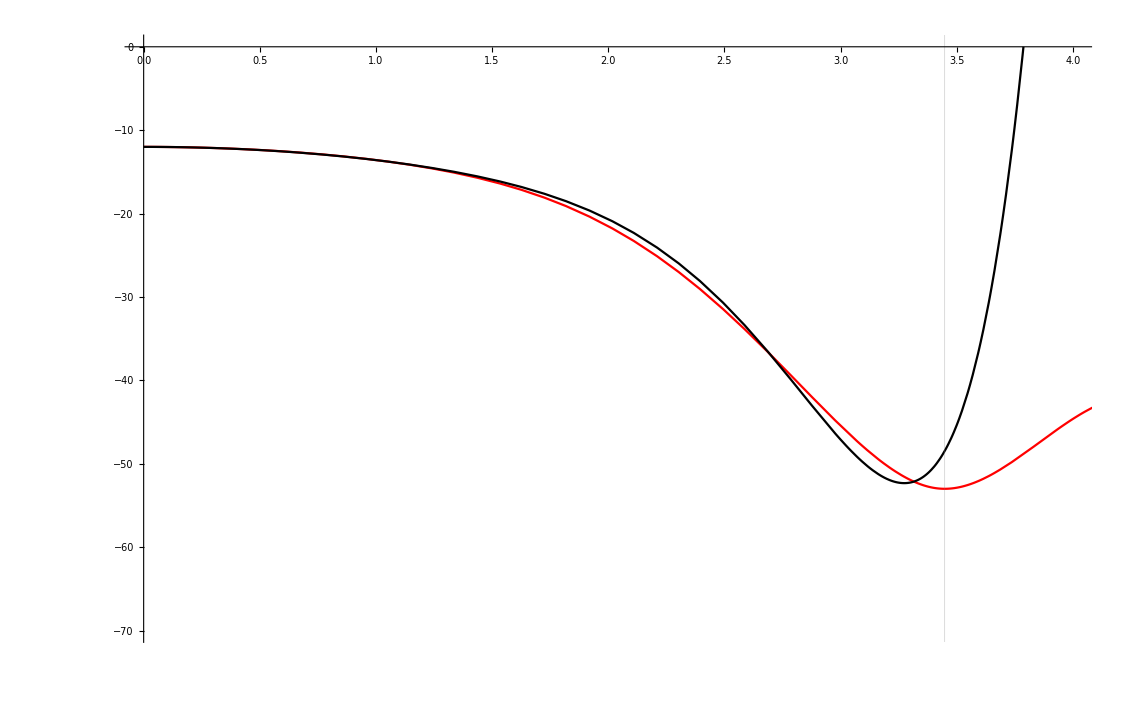

```mathematica
(*Analytical black, reconstructed red *)
Plot[{V[a],1/768 (6 a^2 (8+(2 a^2)/ϕM^2-(3 a^4)/ϕQ)^2-(96+8 a^2+a^4/ϕM^2-a^6/ϕQ)^2)/.{ϕM->0.9,ϕQ->10}},{a,0,4.7},GridLines->{{MinimumReconstructedPotential},None},PlotStyle->{Red,Black},PlotRange->{{0,4},{-70,0}}]
```

#### Im going to calculate the relative error (th-NN)/th for the reconstructed and real potential.

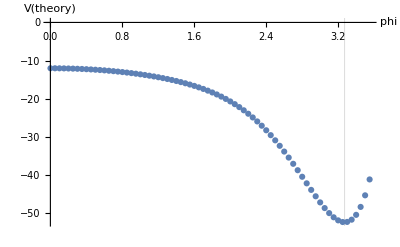

```mathematica
phivalues=Range[0.001,MinimumReconstructedPotential,0.05];
Vthlist = Table[{a,1/768 (6 a^2 (8+(2 a^2)/ϕM^2-(3 a^4)/ϕQ)^2-(96+8 a^2+a^4/ϕM^2-a^6/ϕQ)^2)/.{ϕM->0.9,ϕQ->10}},{a,phivalues}];
Vth=Interpolation[Vthlist];
minimumtheoreticalpotential=FindRoot[Vth'[phi]==0,{phi,3.1}][[1,2]];
a = ListPlot[Vth,AxesLabel->{"phi","V(theory)"},GridLines->{{minimumtheoreticalpotential},None}]
```

```mathematica
Vrecovered = Interpolation[RRR];
```

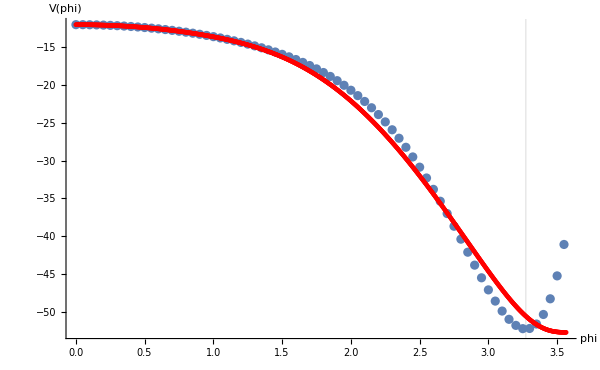

```mathematica
Show[a,ListPlot[Vrecovered,PlotStyle->Red],PlotRange->{{0,4},{-10,-60}}, AxesLabel->{"phi", "V(phi)"}, ImageSize->600]
```

```mathematica
DiffV = {};
```

```mathematica
For[i =0.001, i<=minimumtheoreticalpotential,If[i>=2.1,i+=0.001,i+=0.01], AppendTo[DiffV,{i,Abs[(Abs[Vth[i]-Vrecovered[i]]/Vth[i])*100]}];
]
```

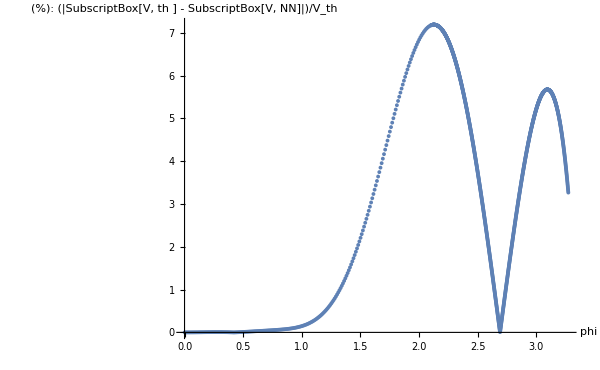

```mathematica
ListPlot[DiffV, AxesLabel->{"phi", "(%): (|SubscriptBox[V, th ] - SubscriptBox[V, NN]|)/V_th"}, ImageSize->600]
```

```mathematica
Export["/Users/pablo/Desktop/NNholo/MH_flattening_paper_3_to_1/flat_5_heads/results_2/pedros_NON_flat/rel_error_V_non_flat.csv",DiffV,"CSV"];
```

#### Equations

```mathematica
ClearAll[AA,hh,ϕϕ,ΦΦ,A,ϕ,h,r,ff,γ,b,L,ϕM];

ff[a_]:=ⅇ^-a
(*V[a_]:=1/768 (6 a^2 (8+(2 a^2)/ϕM^2-(3 a^4)/ϕQ)^2-(96+8 a^2+a^4/ϕM^2-a^6/ϕQ)^2);*)
Veff:=V[ϕϕ[r]]-1/2 ⅇ^(-2AA[r])ff[ϕϕ[r]] ΦΦ'[r]^2;
EOMA=AA''[r]+1/6 ϕϕ'[r]^2;
EOMh=hh''[r]+4AA'[r]hh'[r]-ⅇ^(-2AA[r])ff[ϕϕ[r]] ΦΦ'[r]^2;
EOMΦ=ΦΦ''[r]+2AA'[r]ΦΦ'[r]+D[ff[ϕϕ[r]],ϕϕ[r]]/ff[ϕϕ[r]] ϕϕ'[r]ΦΦ'[r];
EOMϕ=ϕϕ''[r]+(4AA'[r]+hh'[r]/hh[r])ϕϕ'[r]-1/hh[r] D[Veff,ϕϕ[r]];
CONSTRAINT=hh[r](24 AA'[r]^2-ϕϕ'[r]^2)+6AA'[r]hh'[r]+2 V[ϕϕ[r]]+ⅇ^(-2AA[r])ff[ϕϕ[r]] ΦΦ'[r]^2;
```

#### Analytical expansion at the horizon

```mathematica
REP={Subscript[A, 1]->-(ff[ϕH] Subscript[Φ, 1]^2+2 V[ϕH])/(6 h1),Subscript[A, 2]->-((Subscript[Φ, 1]^2 ff'[ϕH]-2 V'[ϕH])^2)/(48 h1^2),Subscript[ϕ, 1]->-(Subscript[Φ, 1]^2 ff'[ϕH]-2 V'[ϕH])/(2 h1),Subscript[h, 2]->1/6 (5 ff[ϕH] Subscript[Φ, 1]^2+4 V[ϕH]),Subscript[Φ, 2]->(Subscript[Φ, 1] (2 ff[ϕH]^2 Subscript[Φ, 1]^2+4 ff[ϕH] V[ϕH]+3 ff'[ϕH] (Subscript[Φ, 1]^2 ff'[ϕH]-2 V'[ϕH])))/(12 h1 ff[ϕH]),Subscript[A, 3]->-1/(288 h1^3 ff[ϕH])(Subscript[Φ, 1]^2 ff'[ϕH]-2 V'[ϕH]) (2 Subscript[Φ, 1]^2 ff'[ϕH]^2 (Subscript[Φ, 1]^2 ff'[ϕH]-2 V'[ϕH])+4 ff[ϕH]^2 Subscript[Φ, 1]^2 V'[ϕH]+ff[ϕH] (-Subscript[Φ, 1]^4 ff'[ϕH] ff''[ϕH]-4 V'[ϕH] V''[ϕH]+2 Subscript[Φ, 1]^2 (2 V[ϕH] ff'[ϕH]+V'[ϕH] ff''[ϕH]+ff'[ϕH] V''[ϕH]))),Subscript[ϕ, 2]->1/(16 h1^2 ff[ϕH])(-2 Subscript[Φ, 1]^2 ff'[ϕH]^2 (Subscript[Φ, 1]^2 ff'[ϕH]-2 V'[ϕH])-4 ff[ϕH]^2 Subscript[Φ, 1]^2 V'[ϕH]+ff[ϕH] (Subscript[Φ, 1]^4 ff'[ϕH] ff''[ϕH]+4 V'[ϕH] V''[ϕH]-2 Subscript[Φ, 1]^2 (2 V[ϕH] ff'[ϕH]+V'[ϕH] ff''[ϕH]+ff'[ϕH] V''[ϕH]))),Subscript[h, 3]->(19 ff[ϕH]^2 Subscript[Φ, 1]^4+46 ff[ϕH] Subscript[Φ, 1]^2 V[ϕH]+16 V[ϕH]^2+6 Subscript[Φ, 1]^4 ff'[ϕH]^2-15 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+6 V'[ϕH]^2)/(54 h1),Subscript[Φ, 3]->1/(432 h1^2 ff[ϕH]^2)Subscript[Φ, 1] (8 ff[ϕH]^4 Subscript[Φ, 1]^4+32 ff[ϕH]^3 Subscript[Φ, 1]^2 V[ϕH]+18 ff'[ϕH]^2 (3 Subscript[Φ, 1]^4 ff'[ϕH]^2-10 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+8 V'[ϕH]^2)+ff[ϕH]^2 (32 V[ϕH]^2+6 (5 Subscript[Φ, 1]^4 ff'[ϕH]^2-6 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+4 V'[ϕH]^2))-3 ff[ϕH] (9 Subscript[Φ, 1]^4 ff'[ϕH]^2 ff''[ϕH]+4 V'[ϕH] (8 V[ϕH] ff'[ϕH]+6 V'[ϕH] ff''[ϕH]+3 ff'[ϕH] V''[ϕH])-2 Subscript[Φ, 1]^2 ff'[ϕH] (14 V[ϕH] ff'[ϕH]+15 V'[ϕH] ff''[ϕH]+3 ff'[ϕH] V''[ϕH]))),Subscript[A, 4]->1/(41472 h1^4 ff[ϕH]^2)(16 ff[ϕH]^4 Subscript[Φ, 1]^4 (5 Subscript[Φ, 1]^2 ff'[ϕH]-19 V'[ϕH]) V'[ϕH]-12 ff'[ϕH]^3 (11 Subscript[Φ, 1]^2 ff'[ϕH]-12 V'[ϕH]) (Subscript[Φ, 1]^3 ff'[ϕH]-2 Subscript[Φ, 1] V'[ϕH])^2+4 ff[ϕH] Subscript[Φ, 1]^2 ff'[ϕH] (Subscript[Φ, 1]^2 ff'[ϕH]-2 V'[ϕH]) (33 Subscript[Φ, 1]^4 ff'[ϕH]^2 ff''[ϕH]+4 V'[ϕH] (20 V[ϕH] ff'[ϕH]+18 V'[ϕH] ff''[ϕH]+15 ff'[ϕH] V''[ϕH])-2 Subscript[Φ, 1]^2 ff'[ϕH] (44 V[ϕH] ff'[ϕH]+51 V'[ϕH] ff''[ϕH]+15 ff'[ϕH] V''[ϕH]))+4 ff[ϕH]^3 (Subscript[Φ, 1]^8 ff'[ϕH]^2 ff''[ϕH]+8 Subscript[Φ, 1]^2 V'[ϕH]^2 (8 V[ϕH]+23 V''[ϕH])+2 Subscript[Φ, 1]^6 ff'[ϕH] (10 V[ϕH] ff'[ϕH]+10 V'[ϕH] ff''[ϕH]+11 ff'[ϕH] V''[ϕH])-4 Subscript[Φ, 1]^4 V'[ϕH] (36 V[ϕH] ff'[ϕH]+11 V'[ϕH] ff''[ϕH]+34 ff'[ϕH] V''[ϕH]))+ff[ϕH]^2 (-Subscript[Φ, 1]^8 ff'[ϕH]^2 (4 ff'[ϕH]^2+15 ff''[ϕH]^2+12 ff'[ϕH] Derivative[3][ff][ϕH])-16 V'[ϕH]^2 (8 V'[ϕH]^2+V''[ϕH] (-8 V[ϕH]+15 V''[ϕH])+12 V'[ϕH] Derivative[3][V][ϕH])+4 Subscript[Φ, 1]^6 ff'[ϕH] (15 V'[ϕH] ff''[ϕH]^2+ff'[ϕH] (44 V[ϕH] ff''[ϕH]+15 ff''[ϕH] V''[ϕH]+18 V'[ϕH] Derivative[3][ff][ϕH])+6 ff'[ϕH]^2 (-7 V'[ϕH]+Derivative[3][V][ϕH]))+16 Subscript[Φ, 1]^2 V'[ϕH] (16 V[ϕH]^2 ff'[ϕH]+4 V[ϕH] (5 V'[ϕH] ff''[ϕH]+4 ff'[ϕH] V''[ϕH])+3 V'[ϕH] (5 ff''[ϕH] V''[ϕH]+2 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (10 V'[ϕH]^2+15 V''[ϕH]^2+18 V'[ϕH] Derivative[3][V][ϕH]))-4 Subscript[Φ, 1]^4 (68 V[ϕH]^2 ff'[ϕH]^2+15 V'[ϕH]^2 ff''[ϕH]^2+8 V[ϕH] ff'[ϕH] (16 V'[ϕH] ff''[ϕH]+5 ff'[ϕH] V''[ϕH])+12 ff'[ϕH] V'[ϕH] (5 ff''[ϕH] V''[ϕH]+3 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-76 V'[ϕH]^2+15 V''[ϕH]^2+36 V'[ϕH] Derivative[3][V][ϕH])))),Subscript[ϕ, 3]->1/(864 h1^3 ff[ϕH]^2)(40 ff[ϕH]^4 Subscript[Φ, 1]^4 V'[ϕH]-24 Subscript[Φ, 1]^2 ff'[ϕH]^3 (2 Subscript[Φ, 1]^4 ff'[ϕH]^2-7 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+6 V'[ϕH]^2)+8 ff[ϕH] Subscript[Φ, 1]^2 ff'[ϕH] (6 Subscript[Φ, 1]^4 ff'[ϕH]^2 ff''[ϕH]+2 V'[ϕH] (10 V[ϕH] ff'[ϕH]+9 V'[ϕH] ff''[ϕH]+3 ff'[ϕH] V''[ϕH])-Subscript[Φ, 1]^2 ff'[ϕH] (13 V[ϕH] ff'[ϕH]+21 V'[ϕH] ff''[ϕH]+3 ff'[ϕH] V''[ϕH]))+2 ff[ϕH]^3 (Subscript[Φ, 1]^6 ff'[ϕH] ff''[ϕH]-8 Subscript[Φ, 1]^2 V'[ϕH] (4 V[ϕH]+7 V''[ϕH])+Subscript[Φ, 1]^4 (20 V[ϕH] ff'[ϕH]+4 V'[ϕH] ff''[ϕH]+22 ff'[ϕH] V''[ϕH]))-ff[ϕH]^2 (Subscript[Φ, 1]^6 ff'[ϕH] (2 ff'[ϕH]^2+3 ff''[ϕH]^2+6 ff'[ϕH] Derivative[3][ff][ϕH])+2 Subscript[Φ, 1]^4 (-3 V'[ϕH] ff''[ϕH]^2-2 ff'[ϕH] (13 V[ϕH] ff''[ϕH]+3 ff''[ϕH] V''[ϕH]+6 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (8 V'[ϕH]-6 Derivative[3][V][ϕH]))-8 V'[ϕH] (4 V'[ϕH]^2+V''[ϕH] (-4 V[ϕH]+3 V''[ϕH])+6 V'[ϕH] Derivative[3][V][ϕH])+4 Subscript[Φ, 1]^2 (16 V[ϕH]^2 ff'[ϕH]+2 V[ϕH] (10 V'[ϕH] ff''[ϕH]+ff'[ϕH] V''[ϕH])+6 V'[ϕH] (ff''[ϕH] V''[ϕH]+V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH] (2 V'[ϕH]^2+V''[ϕH]^2+4 V'[ϕH] Derivative[3][V][ϕH])))),Subscript[h, 4]->1/(5184 h1^2 ff[ϕH])(520 ff[ϕH]^4 Subscript[Φ, 1]^6+2208 ff[ϕH]^3 Subscript[Φ, 1]^4 V[ϕH]+54 ff[ϕH]^2 Subscript[Φ, 1]^2 (48 V[ϕH]^2+9 Subscript[Φ, 1]^4 ff'[ϕH]^2-22 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+12 V'[ϕH]^2)+18 Subscript[Φ, 1]^2 ff'[ϕH]^2 (11 Subscript[Φ, 1]^4 ff'[ϕH]^2-38 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+32 V'[ϕH]^2)+ff[ϕH] (512 V[ϕH]^3+36 V[ϕH] (25 Subscript[Φ, 1]^4 ff'[ϕH]^2-52 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+16 V'[ϕH]^2)-9 (Subscript[Φ, 1]^2 ff'[ϕH]-2 V'[ϕH]) (11 Subscript[Φ, 1]^4 ff'[ϕH] ff''[ϕH]+8 V'[ϕH] V''[ϕH]-2 Subscript[Φ, 1]^2 (8 V'[ϕH] ff''[ϕH]+5 ff'[ϕH] V''[ϕH])))),Subscript[Φ, 4]->1/(5184 h1^3 ff[ϕH]^3)Subscript[Φ, 1] (8 ff[ϕH]^6 Subscript[Φ, 1]^6+48 ff[ϕH]^5 Subscript[Φ, 1]^4 V[ϕH]+6 ff[ϕH]^4 (16 Subscript[Φ, 1]^2 V[ϕH]^2+9 Subscript[Φ, 1]^6 ff'[ϕH]^2-10 Subscript[Φ, 1]^4 ff'[ϕH] V'[ϕH])+36 ff'[ϕH]^3 (11 Subscript[Φ, 1]^6 ff'[ϕH]^3-52 Subscript[Φ, 1]^4 ff'[ϕH]^2 V'[ϕH]+78 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]^2-36 V'[ϕH]^3)+ff[ϕH]^3 (64 V[ϕH]^3+24 V[ϕH] (11 Subscript[Φ, 1]^4 ff'[ϕH]^2-8 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+6 V'[ϕH]^2)-93 Subscript[Φ, 1]^6 ff'[ϕH]^2 ff''[ϕH]+72 V'[ϕH]^2 V''[ϕH]+12 Subscript[Φ, 1]^2 V'[ϕH] (6 V'[ϕH] ff''[ϕH]-ff'[ϕH] V''[ϕH])+6 Subscript[Φ, 1]^4 ff'[ϕH] (22 V'[ϕH] ff''[ϕH]+ff'[ϕH] V''[ϕH]))-6 ff[ϕH] ff'[ϕH] (66 Subscript[Φ, 1]^6 ff'[ϕH]^3 ff''[ϕH]-36 V'[ϕH]^2 (4 V[ϕH] ff'[ϕH]+6 V'[ϕH] ff''[ϕH]+3 ff'[ϕH] V''[ϕH])+4 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH] (82 V[ϕH] ff'[ϕH]+117 V'[ϕH] ff''[ϕH]+30 ff'[ϕH] V''[ϕH])-Subscript[Φ, 1]^4 ff'[ϕH]^2 (134 V[ϕH] ff'[ϕH]+312 V'[ϕH] ff''[ϕH]+33 ff'[ϕH] V''[ϕH]))+3 ff[ϕH]^2 (Subscript[Φ, 1]^6 ff'[ϕH]^2 (70 ff'[ϕH]^2+15 ff''[ϕH]^2+12 ff'[ϕH] Derivative[3][ff][ϕH])-Subscript[Φ, 1]^4 ff'[ϕH] (57 V'[ϕH] ff''[ϕH]^2+ff'[ϕH] (134 V[ϕH] ff''[ϕH]+33 ff''[ϕH] V''[ϕH]+66 V'[ϕH] Derivative[3][ff][ϕH])+2 ff'[ϕH]^2 (71 V'[ϕH]+3 Derivative[3][V][ϕH]))+2 Subscript[Φ, 1]^2 (76 V[ϕH]^2 ff'[ϕH]^2+27 V'[ϕH]^2 ff''[ϕH]^2+4 V[ϕH] ff'[ϕH] (41 V'[ϕH] ff''[ϕH]+5 ff'[ϕH] V''[ϕH])+60 ff'[ϕH] V'[ϕH] (ff''[ϕH] V''[ϕH]+V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH]^2 (12 V'[ϕH]^2+V''[ϕH]^2+4 V'[ϕH] Derivative[3][V][ϕH]))-4 V'[ϕH] (24 V[ϕH]^2 ff'[ϕH]+2 V[ϕH] (18 V'[ϕH] ff''[ϕH]+7 ff'[ϕH] V''[ϕH])+9 V'[ϕH] (3 ff''[ϕH] V''[ϕH]+2 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (22 V'[ϕH]^2+3 V''[ϕH]^2+6 V'[ϕH] Derivative[3][V][ϕH])))),Subscript[A, 5]->-1/(829440 h1^5 ff[ϕH]^3)(192 ff[ϕH]^6 Subscript[Φ, 1]^6 (Subscript[Φ, 1]^2 ff'[ϕH]-7 V'[ϕH]) V'[ϕH]+12 ff'[ϕH]^4 (Subscript[Φ, 1]^3 ff'[ϕH]-2 Subscript[Φ, 1] V'[ϕH])^2 (119 Subscript[Φ, 1]^4 ff'[ϕH]^2-282 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+144 V'[ϕH]^2)+16 ff[ϕH]^5 (10 Subscript[Φ, 1]^4 V'[ϕH]^2 (24 V[ϕH]+37 V''[ϕH])+Subscript[Φ, 1]^8 ff'[ϕH] (12 V[ϕH] ff'[ϕH]+13 V'[ϕH] ff''[ϕH]+21 ff'[ϕH] V''[ϕH])-Subscript[Φ, 1]^6 V'[ϕH] (216 V[ϕH] ff'[ϕH]+44 V'[ϕH] ff''[ϕH]+209 ff'[ϕH] V''[ϕH]))-2 ff[ϕH] Subscript[Φ, 1]^2 ff'[ϕH]^2 (Subscript[Φ, 1]^2 ff'[ϕH]-2 V'[ϕH]) (1071 Subscript[Φ, 1]^6 ff'[ϕH]^3 ff''[ϕH]-72 V'[ϕH]^2 (28 V[ϕH] ff'[ϕH]+36 V'[ϕH] ff''[ϕH]+23 ff'[ϕH] V''[ϕH])-2 Subscript[Φ, 1]^4 ff'[ϕH]^2 (1150 V[ϕH] ff'[ϕH]+2340 V'[ϕH] ff''[ϕH]+333 ff'[ϕH] V''[ϕH])+4 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH] (1246 V[ϕH] ff'[ϕH]+1593 V'[ϕH] ff''[ϕH]+540 ff'[ϕH] V''[ϕH]))+2 ff[ϕH]^2 Subscript[Φ, 1]^2 (Subscript[Φ, 1]^8 ff'[ϕH]^4 (44 ff'[ϕH]^2+324 ff''[ϕH]^2+141 ff'[ϕH] Derivative[3][ff][ϕH])+2 Subscript[Φ, 1]^6 ff'[ϕH]^3 (-963 V'[ϕH] ff''[ϕH]^2-ff'[ϕH] (1150 V[ϕH] ff''[ϕH]+333 ff''[ϕH] V''[ϕH]+495 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (360 V'[ϕH]-69 Derivative[3][V][ϕH]))+16 V'[ϕH]^2 (120 V[ϕH]^2 ff'[ϕH]^2+54 V'[ϕH]^2 ff''[ϕH]^2+2 V[ϕH] ff'[ϕH] (126 V'[ϕH] ff''[ϕH]+71 ff'[ϕH] V''[ϕH])+9 ff'[ϕH] V'[ϕH] (23 ff''[ϕH] V''[ϕH]+8 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (82 V'[ϕH]^2+63 V''[ϕH]^2+69 V'[ϕH] Derivative[3][V][ϕH]))+4 Subscript[Φ, 1]^4 ff'[ϕH]^2 (628 V[ϕH]^2 ff'[ϕH]^2+1008 V'[ϕH]^2 ff''[ϕH]^2+2 V[ϕH] ff'[ϕH] (1198 V'[ϕH] ff''[ϕH]+149 ff'[ϕH] V''[ϕH])+9 ff'[ϕH] V'[ϕH] (97 ff''[ϕH] V''[ϕH]+71 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-614 V'[ϕH]^2+63 V''[ϕH]^2+207 V'[ϕH] Derivative[3][V][ϕH]))-8 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH] (676 V[ϕH]^2 ff'[ϕH]^2+423 V'[ϕH]^2 ff''[ϕH]^2+2 V[ϕH] ff'[ϕH] (749 V'[ϕH] ff''[ϕH]+220 ff'[ϕH] V''[ϕH])+3 ff'[ϕH] V'[ϕH] (249 ff''[ϕH] V''[ϕH]+119 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-128 V'[ϕH]^2+126 V''[ϕH]^2+207 V'[ϕH] Derivative[3][V][ϕH])))+4 ff[ϕH]^4 Subscript[Φ, 1]^2 (Subscript[Φ, 1]^8 ff'[ϕH]^2 (5 ff''[ϕH]^2+3 ff'[ϕH] Derivative[3][ff][ϕH])-8 V'[ϕH]^2 (24 V[ϕH]^2+90 V'[ϕH]^2+44 V[ϕH] V''[ϕH]+140 V''[ϕH]^2+111 V'[ϕH] Derivative[3][V][ϕH])+Subscript[Φ, 1]^6 ff'[ϕH] (19 V'[ϕH] ff''[ϕH]^2+ff'[ϕH] (100 V[ϕH] ff''[ϕH]+91 ff''[ϕH] V''[ϕH]+45 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-122 V'[ϕH]+48 Derivative[3][V][ϕH]))-2 Subscript[Φ, 1]^4 (264 V[ϕH]^2 ff'[ϕH]^2+29 V'[ϕH]^2 ff''[ϕH]^2+2 V[ϕH] ff'[ϕH] (219 V'[ϕH] ff''[ϕH]+137 ff'[ϕH] V''[ϕH])+4 ff'[ϕH] V'[ϕH] (65 ff''[ϕH] V''[ϕH]+27 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-122 V'[ϕH]^2+101 V''[ϕH]^2+207 V'[ϕH] Derivative[3][V][ϕH]))+4 Subscript[Φ, 1]^2 V'[ϕH] (360 V[ϕH]^2 ff'[ϕH]+V[ϕH] (266 V'[ϕH] ff''[ϕH]+390 ff'[ϕH] V''[ϕH])+V'[ϕH] (169 ff''[ϕH] V''[ϕH]+57 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (162 V'[ϕH]^2+241 V''[ϕH]^2+270 V'[ϕH] Derivative[3][V][ϕH])))-ff[ϕH]^3 (3 Subscript[Φ, 1]^10 ff'[ϕH]^2 (7 ff''[ϕH]^3+23 ff'[ϕH] ff''[ϕH] Derivative[3][ff][ϕH]+ff'[ϕH]^2 (40 ff''[ϕH]+6 Derivative[4][ff][ϕH]))+2 Subscript[Φ, 1]^8 ff'[ϕH] (-42 V'[ϕH] ff''[ϕH]^3+2 V[ϕH] ff'[ϕH] (254 ff'[ϕH]^2-130 ff''[ϕH]^2-105 ff'[ϕH] Derivative[3][ff][ϕH])-9 ff'[ϕH] ff''[ϕH] (7 ff''[ϕH] V''[ϕH]+23 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-69 (V''[ϕH] Derivative[3][ff][ϕH]+ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH] (706 ff''[ϕH]-72 Derivative[4][ff][ϕH]))+18 ff'[ϕH]^3 (23 V''[ϕH]-Derivative[4][V][ϕH]))-32 V'[ϕH]^2 (V''[ϕH]^2 (-40 V[ϕH]+21 V''[ϕH])+3 V'[ϕH] (-8 V[ϕH]+23 V''[ϕH]) Derivative[3][V][ϕH]+2 V'[ϕH]^2 (32 V''[ϕH]+9 Derivative[4][V][ϕH]))+16 Subscript[Φ, 1]^2 V'[ϕH] (48 V[ϕH]^3 ff'[ϕH]+42 ff'[ϕH] V''[ϕH]^3+40 V[ϕH]^2 (3 V'[ϕH] ff''[ϕH]+ff'[ϕH] V''[ϕH])+9 V'[ϕH] V''[ϕH] (7 ff''[ϕH] V''[ϕH]+23 ff'[ϕH] Derivative[3][V][ϕH])+2 V[ϕH] (V'[ϕH] (71 ff''[ϕH] V''[ϕH]+42 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (54 V'[ϕH]^2-V''[ϕH]^2+27 V'[ϕH] Derivative[3][V][ϕH]))+2 V'[ϕH]^3 (41 ff''[ϕH]+9 Derivative[4][ff][ϕH])+V'[ϕH]^2 (69 (V''[ϕH] Derivative[3][ff][ϕH]+ff''[ϕH] Derivative[3][V][ϕH])+2 ff'[ϕH] (71 V''[ϕH]+36 Derivative[4][V][ϕH])))+4 Subscript[Φ, 1]^6 (628 V[ϕH]^2 ff'[ϕH]^2 ff''[ϕH]+21 V'[ϕH]^2 ff''[ϕH]^3+9 ff'[ϕH] V'[ϕH] ff''[ϕH] (14 ff''[ϕH] V''[ϕH]+23 V'[ϕH] Derivative[3][ff][ϕH])+2 V[ϕH] ff'[ϕH] (221 V'[ϕH] ff''[ϕH]^2+ff'[ϕH] (149 ff''[ϕH] V''[ϕH]+252 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-930 V'[ϕH]+51 Derivative[3][V][ϕH]))+ff'[ϕH]^2 (63 ff''[ϕH] V''[ϕH]^2+207 V'[ϕH] (V''[ϕH] Derivative[3][ff][ϕH]+ff''[ϕH] Derivative[3][V][ϕH])-2 V'[ϕH]^2 (689 ff''[ϕH]-54 Derivative[4][ff][ϕH]))+ff'[ϕH]^3 (69 V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH] (-1126 V''[ϕH]+72 Derivative[4][V][ϕH])))-8 Subscript[Φ, 1]^4 (240 V[ϕH]^3 ff'[ϕH]^2+4 V[ϕH]^2 ff'[ϕH] (169 V'[ϕH] ff''[ϕH]+28 ff'[ϕH] V''[ϕH])+3 V'[ϕH]^2 ff''[ϕH] (21 ff''[ϕH] V''[ϕH]+23 V'[ϕH] Derivative[3][ff][ϕH])+V[ϕH] (182 V'[ϕH]^2 ff''[ϕH]^2+2 ff'[ϕH] V'[ϕH] (220 ff''[ϕH] V''[ϕH]+189 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-956 V'[ϕH]^2+38 V''[ϕH]^2+180 V'[ϕH] Derivative[3][V][ϕH]))+ff'[ϕH] V'[ϕH] (126 ff''[ϕH] V''[ϕH]^2+207 V'[ϕH] (V''[ϕH] Derivative[3][ff][ϕH]+ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (-470 ff''[ϕH]+72 Derivative[4][ff][ϕH]))+ff'[ϕH]^2 (21 V''[ϕH]^3+207 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH]^2 (-634 V''[ϕH]+108 Derivative[4][V][ϕH]))))),Subscript[ϕ, 4]->1/(27648 h1^4 ff[ϕH]^3)(-192 ff[ϕH]^6 Subscript[Φ, 1]^6 V'[ϕH]+12 Subscript[Φ, 1]^2 ff'[ϕH]^4 (-71 Subscript[Φ, 1]^6 ff'[ϕH]^3+352 Subscript[Φ, 1]^4 ff'[ϕH]^2 V'[ϕH]-564 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]^2+288 V'[ϕH]^3)-16 ff[ϕH]^5 (-Subscript[Φ, 1]^4 V'[ϕH] (72 V[ϕH]+71 V''[ϕH])+Subscript[Φ, 1]^6 (12 V[ϕH] ff'[ϕH]+V'[ϕH] ff''[ϕH]+21 ff'[ϕH] V''[ϕH]))+2 ff[ϕH] Subscript[Φ, 1]^2 ff'[ϕH]^2 (639 Subscript[Φ, 1]^6 ff'[ϕH]^3 ff''[ϕH]-72 V'[ϕH]^2 (28 V[ϕH] ff'[ϕH]+36 V'[ϕH] ff''[ϕH]+11 ff'[ϕH] V''[ϕH])-2 Subscript[Φ, 1]^4 ff'[ϕH]^2 (550 V[ϕH] ff'[ϕH]+1584 V'[ϕH] ff''[ϕH]+117 ff'[ϕH] V''[ϕH])+4 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH] (790 V[ϕH] ff'[ϕH]+27 (47 V'[ϕH] ff''[ϕH]+8 ff'[ϕH] V''[ϕH])))-4 ff[ϕH]^4 (Subscript[Φ, 1]^8 ff'[ϕH] (2 ff''[ϕH]^2+3 ff'[ϕH] Derivative[3][ff][ϕH])+4 Subscript[Φ, 1]^2 V'[ϕH] (24 V[ϕH]^2+66 V'[ϕH]^2+20 V[ϕH] V''[ϕH]+38 V''[ϕH]^2+75 V'[ϕH] Derivative[3][V][ϕH])+Subscript[Φ, 1]^6 (-V'[ϕH] ff''[ϕH]^2+ff'[ϕH] (52 V[ϕH] ff''[ϕH]+31 ff''[ϕH] V''[ϕH]+15 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-14 V'[ϕH]+48 Derivative[3][V][ϕH]))-2 Subscript[Φ, 1]^4 (144 V[ϕH]^2 ff'[ϕH]+V[ϕH] (98 V'[ϕH] ff''[ϕH]+82 ff'[ϕH] V''[ϕH])+V'[ϕH] (37 ff''[ϕH] V''[ϕH]+21 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (60 V'[ϕH]^2+35 V''[ϕH]^2+123 V'[ϕH] Derivative[3][V][ϕH])))-2 ff[ϕH]^2 (Subscript[Φ, 1]^8 ff'[ϕH]^3 (32 ff'[ϕH]^2+162 ff''[ϕH]^2+105 ff'[ϕH] Derivative[3][ff][ϕH])+2 Subscript[Φ, 1]^6 ff'[ϕH]^2 (-369 V'[ϕH] ff''[ϕH]^2-ff'[ϕH] (550 V[ϕH] ff''[ϕH]+117 ff''[ϕH] V''[ϕH]+282 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (68 V'[ϕH]-33 Derivative[3][V][ϕH]))-8 Subscript[Φ, 1]^2 V'[ϕH] (120 V[ϕH]^2 ff'[ϕH]^2+54 V'[ϕH]^2 ff''[ϕH]^2+2 V[ϕH] ff'[ϕH] (126 V'[ϕH] ff''[ϕH]+23 ff'[ϕH] V''[ϕH])+9 ff'[ϕH] V'[ϕH] (11 ff''[ϕH] V''[ϕH]+8 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (58 V'[ϕH]^2+9 V''[ϕH]^2+33 V'[ϕH] Derivative[3][V][ϕH]))+4 Subscript[Φ, 1]^4 ff'[ϕH] (220 V[ϕH]^2 ff'[ϕH]^2+2 V[ϕH] ff'[ϕH] (395 V'[ϕH] ff''[ϕH]+29 ff'[ϕH] V''[ϕH])+3 (87 V'[ϕH]^2 ff''[ϕH]^2+ff'[ϕH] V'[ϕH] (72 ff''[ϕH] V''[ϕH]+83 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-10 V'[ϕH]^2+3 V''[ϕH]^2+22 V'[ϕH] Derivative[3][V][ϕH]))))+ff[ϕH]^3 (3 Subscript[Φ, 1]^8 ff'[ϕH] (ff''[ϕH]^3+11 ff'[ϕH] ff''[ϕH] Derivative[3][ff][ϕH]+ff'[ϕH]^2 (28 ff''[ϕH]+6 Derivative[4][ff][ϕH]))+2 Subscript[Φ, 1]^6 (-3 V'[ϕH] ff''[ϕH]^3+2 V[ϕH] ff'[ϕH] (146 ff'[ϕH]^2-34 ff''[ϕH]^2-69 ff'[ϕH] Derivative[3][ff][ϕH])-3 ff'[ϕH] ff''[ϕH] (3 ff''[ϕH] V''[ϕH]+22 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-33 (V''[ϕH] Derivative[3][ff][ϕH]+ff''[ϕH] Derivative[3][V][ϕH])+2 V'[ϕH] (77 ff''[ϕH]-27 Derivative[4][ff][ϕH]))+18 ff'[ϕH]^3 (9 V''[ϕH]-Derivative[4][V][ϕH]))+16 V'[ϕH] (V''[ϕH]^2 (-16 V[ϕH]+3 V''[ϕH])+3 V'[ϕH] (-8 V[ϕH]+11 V''[ϕH]) Derivative[3][V][ϕH]+2 V'[ϕH]^2 (20 V''[ϕH]+9 Derivative[4][V][ϕH]))-8 Subscript[Φ, 1]^2 (48 V[ϕH]^3 ff'[ϕH]+3 ff'[ϕH] V''[ϕH]^3+8 V[ϕH]^2 (15 V'[ϕH] ff''[ϕH]-ff'[ϕH] V''[ϕH])+3 V'[ϕH] V''[ϕH] (3 ff''[ϕH] V''[ϕH]+22 ff'[ϕH] Derivative[3][V][ϕH])+2 V[ϕH] (V'[ϕH] (23 ff''[ϕH] V''[ϕH]+42 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (30 V'[ϕH]^2-5 V''[ϕH]^2+3 V'[ϕH] Derivative[3][V][ϕH]))+2 V'[ϕH]^3 (29 ff''[ϕH]+9 Derivative[4][ff][ϕH])+V'[ϕH]^2 (33 (V''[ϕH] Derivative[3][ff][ϕH]+ff''[ϕH] Derivative[3][V][ϕH])+6 ff'[ϕH] (7 V''[ϕH]+9 Derivative[4][V][ϕH])))+4 Subscript[Φ, 1]^4 (220 V[ϕH]^2 ff'[ϕH] ff''[ϕH]+3 V'[ϕH] ff''[ϕH] (3 ff''[ϕH] V''[ϕH]+11 V'[ϕH] Derivative[3][ff][ϕH])+V[ϕH] (62 V'[ϕH] ff''[ϕH]^2+ff'[ϕH] (58 ff''[ϕH] V''[ϕH]+222 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-416 V'[ϕH]+30 Derivative[3][V][ϕH]))+ff'[ϕH] (9 ff''[ϕH] V''[ϕH]^2+66 V'[ϕH] (V''[ϕH] Derivative[3][ff][ϕH]+ff''[ϕH] Derivative[3][V][ϕH])-6 V'[ϕH]^2 (26 ff''[ϕH]-9 Derivative[4][ff][ϕH]))+ff'[ϕH]^2 (33 V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH] (-184 V''[ϕH]+54 Derivative[4][V][ϕH]))))),Subscript[h, 5]->1/(155520 h1^3 ff[ϕH]^2)(3376 ff[ϕH]^6 Subscript[Φ, 1]^8+20768 ff[ϕH]^5 Subscript[Φ, 1]^6 V[ϕH]+12 ff[ϕH]^4 Subscript[Φ, 1]^4 (3632 V[ϕH]^2+519 Subscript[Φ, 1]^4 ff'[ϕH]^2-1154 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+604 V'[ϕH]^2)+36 Subscript[Φ, 1]^2 ff'[ϕH]^3 (77 Subscript[Φ, 1]^6 ff'[ϕH]^3-368 Subscript[Φ, 1]^4 ff'[ϕH]^2 V'[ϕH]+560 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]^2-264 V'[ϕH]^3)-12 ff[ϕH] Subscript[Φ, 1]^2 ff'[ϕH] (231 Subscript[Φ, 1]^6 ff'[ϕH]^3 ff''[ϕH]+8 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH] (383 V[ϕH] ff'[ϕH]+210 V'[ϕH] ff''[ϕH]+60 ff'[ϕH] V''[ϕH])-4 V'[ϕH]^2 (532 V[ϕH] ff'[ϕH]+198 V'[ϕH] ff''[ϕH]+111 ff'[ϕH] V''[ϕH])-Subscript[Φ, 1]^4 ff'[ϕH]^2 (1018 V[ϕH] ff'[ϕH]+1104 V'[ϕH] ff''[ϕH]+129 ff'[ϕH] V''[ϕH]))+2 ff[ϕH]^3 Subscript[Φ, 1]^2 (16576 V[ϕH]^3+48 V[ϕH] (257 Subscript[Φ, 1]^4 ff'[ϕH]^2-534 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+253 V'[ϕH]^2)-1293 Subscript[Φ, 1]^6 ff'[ϕH]^2 ff''[ϕH]+1992 V'[ϕH]^2 V''[ϕH]+6 Subscript[Φ, 1]^4 ff'[ϕH] (646 V'[ϕH] ff''[ϕH]+173 ff'[ϕH] V''[ϕH])-12 Subscript[Φ, 1]^2 V'[ϕH] (224 V'[ϕH] ff''[ϕH]+247 ff'[ϕH] V''[ϕH]))+ff[ϕH]^2 (4096 V[ϕH]^4+96 V[ϕH]^2 (241 Subscript[Φ, 1]^4 ff'[ϕH]^2-410 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+96 V'[ϕH]^2)-12 V[ϕH] (509 Subscript[Φ, 1]^6 ff'[ϕH]^2 ff''[ϕH]-352 V'[ϕH]^2 V''[ϕH]-4 Subscript[Φ, 1]^4 ff'[ϕH] (383 V'[ϕH] ff''[ϕH]+85 ff'[ϕH] V''[ϕH])+4 Subscript[Φ, 1]^2 V'[ϕH] (266 V'[ϕH] ff''[ϕH]+205 ff'[ϕH] V''[ϕH]))+3 (Subscript[Φ, 1]^8 ff'[ϕH]^2 (2020 ff'[ϕH]^2+105 ff''[ϕH]^2+84 ff'[ϕH] Derivative[3][ff][ϕH])+16 V'[ϕH]^2 (44 V'[ϕH]^2+15 V''[ϕH]^2+12 V'[ϕH] Derivative[3][V][ϕH])-6 Subscript[Φ, 1]^6 ff'[ϕH] (67 V'[ϕH] ff''[ϕH]^2+ff'[ϕH] (43 ff''[ϕH] V''[ϕH]+78 V'[ϕH] Derivative[3][ff][ϕH])+2 ff'[ϕH]^2 (589 V'[ϕH]+5 Derivative[3][V][ϕH]))+32 Subscript[Φ, 1]^4 (12 V'[ϕH]^2 ff''[ϕH]^2+3 ff'[ϕH] V'[ϕH] (10 ff''[ϕH] V''[ϕH]+9 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (244 V'[ϕH]^2+3 V''[ϕH]^2+9 V'[ϕH] Derivative[3][V][ϕH]))-8 Subscript[Φ, 1]^2 V'[ϕH] (3 V'[ϕH] (37 ff''[ϕH] V''[ϕH]+22 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (446 V'[ϕH]^2+39 V''[ϕH]^2+54 V'[ϕH] Derivative[3][V][ϕH]))))),Subscript[Φ, 5]->1/(1244160 h1^4 ff[ϕH]^4)Subscript[Φ, 1] (128 ff[ϕH]^8 Subscript[Φ, 1]^8+1024 ff[ϕH]^7 Subscript[Φ, 1]^6 V[ϕH]+192 ff[ϕH]^6 Subscript[Φ, 1]^4 (16 V[ϕH]^2+7 Subscript[Φ, 1]^4 ff'[ϕH]^2-6 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+7 V'[ϕH]^2)+108 ff'[ϕH]^4 (595 Subscript[Φ, 1]^8 ff'[ϕH]^4-3648 Subscript[Φ, 1]^6 ff'[ϕH]^3 V'[ϕH]+8036 Subscript[Φ, 1]^4 ff'[ϕH]^2 V'[ϕH]^2-7392 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]^3+2304 V'[ϕH]^4)-18 ff[ϕH] ff'[ϕH]^2 (5355 Subscript[Φ, 1]^8 ff'[ϕH]^4 ff''[ϕH]+1152 V'[ϕH]^3 (8 V[ϕH] ff'[ϕH]+18 V'[ϕH] ff''[ϕH]+9 ff'[ϕH] V''[ϕH])-6 Subscript[Φ, 1]^6 ff'[ϕH]^3 (1506 V[ϕH] ff'[ϕH]+5472 V'[ϕH] ff''[ϕH]+391 ff'[ϕH] V''[ϕH])-8 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]^2 (4684 V[ϕH] ff'[ϕH]+8316 V'[ϕH] ff''[ϕH]+2451 ff'[ϕH] V''[ϕH])+4 Subscript[Φ, 1]^4 ff'[ϕH]^2 V'[ϕH] (8614 V[ϕH] ff'[ϕH]+18081 V'[ϕH] ff''[ϕH]+2976 ff'[ϕH] V''[ϕH]))-16 ff[ϕH]^5 Subscript[Φ, 1]^2 (-256 V[ϕH]^3-24 V[ϕH] (25 Subscript[Φ, 1]^4 ff'[ϕH]^2-25 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]-8 V'[ϕH]^2)+3 (71 Subscript[Φ, 1]^6 ff'[ϕH]^2 ff''[ϕH]+88 V'[ϕH]^2 V''[ϕH]-Subscript[Φ, 1]^4 ff'[ϕH] (99 V'[ϕH] ff''[ϕH]+13 ff'[ϕH] V''[ϕH])+Subscript[Φ, 1]^2 V'[ϕH] (118 V'[ϕH] ff''[ϕH]+21 ff'[ϕH] V''[ϕH])))+6 ff[ϕH]^2 (9 Subscript[Φ, 1]^8 ff'[ϕH]^4 (624 ff'[ϕH]^2+540 ff''[ϕH]^2+235 ff'[ϕH] Derivative[3][ff][ϕH])-6 Subscript[Φ, 1]^6 ff'[ϕH]^3 (4653 V'[ϕH] ff''[ϕH]^2+3 ff'[ϕH] (1506 V[ϕH] ff''[ϕH]+391 ff''[ϕH] V''[ϕH]+790 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (2740 V'[ϕH]+129 Derivative[3][V][ϕH]))+96 V'[ϕH]^2 (96 V[ϕH]^2 ff'[ϕH]^2+108 V'[ϕH]^2 ff''[ϕH]^2+16 V[ϕH] ff'[ϕH] (18 V'[ϕH] ff''[ϕH]+7 ff'[ϕH] V''[ϕH])+36 ff'[ϕH] V'[ϕH] (9 ff''[ϕH] V''[ϕH]+4 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (104 V'[ϕH]^2+51 V''[ϕH]^2+48 V'[ϕH] Derivative[3][V][ϕH]))+4 Subscript[Φ, 1]^4 ff'[ϕH]^2 (5500 V[ϕH]^2 ff'[ϕH]^2+14013 V'[ϕH]^2 ff''[ϕH]^2+6 V[ϕH] ff'[ϕH] (4307 V'[ϕH] ff''[ϕH]+329 ff'[ϕH] V''[ϕH])+9 ff'[ϕH] V'[ϕH] (992 ff''[ϕH] V''[ϕH]+971 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH]^2 (962 V'[ϕH]^2+111 V''[ϕH]^2+354 V'[ϕH] Derivative[3][V][ϕH]))-8 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH] (4936 V[ϕH]^2 ff'[ϕH]^2+5562 V'[ϕH]^2 ff''[ϕH]^2+6 V[ϕH] ff'[ϕH] (2342 V'[ϕH] ff''[ϕH]+435 ff'[ϕH] V''[ϕH])+9 ff'[ϕH] V'[ϕH] (817 ff''[ϕH] V''[ϕH]+512 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (870 V'[ϕH]^2+639 V''[ϕH]^2+963 V'[ϕH] Derivative[3][V][ϕH])))+4 ff[ϕH]^4 (512 V[ϕH]^4+144 V[ϕH]^2 (37 Subscript[Φ, 1]^4 ff'[ϕH]^2-18 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+16 V'[ϕH]^2)-12 V[ϕH] (453 Subscript[Φ, 1]^6 ff'[ϕH]^2 ff''[ϕH]-160 V'[ϕH]^2 V''[ϕH]-4 Subscript[Φ, 1]^2 V'[ϕH] (124 V'[ϕH] ff''[ϕH]+7 ff'[ϕH] V''[ϕH])+Subscript[Φ, 1]^4 ff'[ϕH] (-169 V'[ϕH] ff''[ϕH]+51 ff'[ϕH] V''[ϕH]))+3 (Subscript[Φ, 1]^8 ff'[ϕH]^2 (710 ff'[ϕH]^2+285 ff''[ϕH]^2+213 ff'[ϕH] Derivative[3][ff][ϕH])+16 V'[ϕH]^2 (26 V'[ϕH]^2+15 V''[ϕH]^2+12 V'[ϕH] Derivative[3][V][ϕH])+Subscript[Φ, 1]^6 ff'[ϕH] (-603 V'[ϕH] ff''[ϕH]^2+ff'[ϕH] (33 ff''[ϕH] V''[ϕH]-435 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-1306 V'[ϕH]+24 Derivative[3][V][ϕH]))+2 Subscript[Φ, 1]^4 (42 V'[ϕH]^2 ff''[ϕH]^2-3 ff'[ϕH] V'[ϕH] (185 ff''[ϕH] V''[ϕH]+109 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (484 V'[ϕH]^2-27 V''[ϕH]^2-105 V'[ϕH] Derivative[3][V][ϕH]))+4 Subscript[Φ, 1]^2 V'[ϕH] (168 V'[ϕH] (3 ff''[ϕH] V''[ϕH]+2 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (166 V'[ϕH]^2+6 V''[ϕH]^2+57 V'[ϕH] Derivative[3][V][ϕH]))))-3 ff[ϕH]^3 (3 Subscript[Φ, 1]^8 ff'[ϕH]^2 (105 ff''[ϕH]^3+345 ff'[ϕH] ff''[ϕH] Derivative[3][ff][ϕH]+ff'[ϕH]^2 (3484 ff''[ϕH]+90 Derivative[4][ff][ϕH]))-8 Subscript[Φ, 1]^2 (1488 V[ϕH]^3 ff'[ϕH]^2+8 V[ϕH]^2 ff'[ϕH] (617 V'[ϕH] ff''[ϕH]+41 ff'[ϕH] V''[ϕH])+36 V'[ϕH]^2 ff''[ϕH] (17 ff''[ϕH] V''[ϕH]+26 V'[ϕH] Derivative[3][ff][ϕH])+2 V[ϕH] (912 V'[ϕH]^2 ff''[ϕH]^2+3 ff'[ϕH] V'[ϕH] (435 ff''[ϕH] V''[ϕH]+578 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (562 V'[ϕH]^2+33 V''[ϕH]^2+201 V'[ϕH] Derivative[3][V][ϕH]))+3 ff'[ϕH] V'[ϕH] (213 ff''[ϕH] V''[ϕH]^2+V'[ϕH] (681 V''[ϕH] Derivative[3][ff][ϕH]+321 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (-382 ff''[ϕH]+306 Derivative[4][ff][ϕH]))+9 ff'[ϕH]^2 (V''[ϕH]^3+22 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]-6 V'[ϕH]^2 (7 V''[ϕH]-3 Derivative[4][V][ϕH])))-2 Subscript[Φ, 1]^6 ff'[ϕH] (621 V'[ϕH] ff''[ϕH]^3+2 V[ϕH] ff'[ϕH] (4258 ff'[ϕH]^2+1530 ff''[ϕH]^2+1239 ff'[ϕH] Derivative[3][ff][ϕH])+9 ff'[ϕH] ff''[ϕH] (71 ff''[ϕH] V''[ϕH]+334 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH]^2 (3 (83 V''[ϕH] Derivative[3][ff][ϕH]+43 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH] (4414 ff''[ϕH]+342 Derivative[4][ff][ϕH]))+6 ff'[ϕH]^3 (43 V''[ϕH]+9 Derivative[4][V][ϕH]))+16 V'[ϕH] (256 V[ϕH]^3 ff'[ϕH]+9 ff'[ϕH] V''[ϕH]^3+32 V[ϕH]^2 (18 V'[ϕH] ff''[ϕH]+5 ff'[ϕH] V''[ϕH])+9 V'[ϕH] V''[ϕH] (34 ff''[ϕH] V''[ϕH]+11 ff'[ϕH] Derivative[3][V][ϕH])+8 V[ϕH] (12 V'[ϕH] (7 ff''[ϕH] V''[ϕH]+6 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (88 V'[ϕH]^2+6 V''[ϕH]^2+15 V'[ϕH] Derivative[3][V][ϕH]))+24 V'[ϕH]^3 (26 ff''[ϕH]+9 Derivative[4][ff][ϕH])+6 V'[ϕH]^2 (12 (9 V''[ϕH] Derivative[3][ff][ϕH]+4 ff''[ϕH] Derivative[3][V][ϕH])+ff'[ϕH] (104 V''[ϕH]+9 Derivative[4][V][ϕH])))+4 Subscript[Φ, 1]^4 (5500 V[ϕH]^2 ff'[ϕH]^2 ff''[ϕH]+2 V[ϕH] ff'[ϕH] (2433 V'[ϕH] ff''[ϕH]^2+3 ff'[ϕH] (329 ff''[ϕH] V''[ϕH]+895 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (2512 V'[ϕH]+141 Derivative[3][V][ϕH]))+3 (102 V'[ϕH]^2 ff''[ϕH]^3+3 ff'[ϕH] V'[ϕH] ff''[ϕH] (139 ff''[ϕH] V''[ϕH]+323 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (111 ff''[ϕH] V''[ϕH]^2+6 V'[ϕH] (119 V''[ϕH] Derivative[3][ff][ϕH]+59 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (364 ff''[ϕH]+486 Derivative[4][ff][ϕH]))+ff'[ϕH]^3 (33 V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH] (-272 V''[ϕH]+54 Derivative[4][V][ϕH])))))),Subscript[A, 6]->1/(447897600 h1^6 ff[ϕH]^4)(640 ff[ϕH]^8 Subscript[Φ, 1]^8 (17 Subscript[Φ, 1]^2 ff'[ϕH]-217 V'[ϕH]) V'[ϕH]-648 ff'[ϕH]^5 (Subscript[Φ, 1]^3 ff'[ϕH]-2 Subscript[Φ, 1] V'[ϕH])^2 (713 Subscript[Φ, 1]^6 ff'[ϕH]^3-2646 Subscript[Φ, 1]^4 ff'[ϕH]^2 V'[ϕH]+2976 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]^2-960 V'[ϕH]^3)-32 ff[ϕH]^7 Subscript[Φ, 1]^6 (Subscript[Φ, 1]^6 ff'[ϕH]^2 ff''[ϕH]-160 V'[ϕH]^2 (177 V[ϕH]+194 V''[ϕH])-2 Subscript[Φ, 1]^4 ff'[ϕH] (170 V[ϕH] ff'[ϕH]+203 V'[ϕH] ff''[ϕH]+412 ff'[ϕH] V''[ϕH])+2 Subscript[Φ, 1]^2 V'[ϕH] (6640 V[ϕH] ff'[ϕH]+944 V'[ϕH] ff''[ϕH]+6829 ff'[ϕH] V''[ϕH]))+144 ff[ϕH] Subscript[Φ, 1]^2 ff'[ϕH]^3 (Subscript[Φ, 1]^2 ff'[ϕH]-2 V'[ϕH]) (6417 Subscript[Φ, 1]^8 ff'[ϕH]^4 ff''[ϕH]+432 V'[ϕH]^3 (24 V[ϕH] ff'[ϕH]+40 V'[ϕH] ff''[ϕH]+23 ff'[ϕH] V''[ϕH])-12 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]^2 (3506 V[ϕH] ff'[ϕH]+5184 V'[ϕH] ff''[ϕH]+1827 ff'[ϕH] V''[ϕH])-Subscript[Φ, 1]^6 ff'[ϕH]^3 (12035 V[ϕH] ff'[ϕH]+36648 V'[ϕH] ff''[ϕH]+3249 ff'[ϕH] V''[ϕH])+2 Subscript[Φ, 1]^4 ff'[ϕH]^2 V'[ϕH] (21011 V[ϕH] ff'[ϕH]+37206 V'[ϕH] ff''[ϕH]+7488 ff'[ϕH] V''[ϕH]))-18 ff[ϕH]^2 Subscript[Φ, 1]^2 ff'[ϕH] (3 Subscript[Φ, 1]^10 ff'[ϕH]^5 (776 ff'[ϕH]^2+8865 ff''[ϕH]^2+2646 ff'[ϕH] Derivative[3][ff][ϕH])+2 Subscript[Φ, 1]^8 ff'[ϕH]^4 (-99333 V'[ϕH] ff''[ϕH]^2-6 ff'[ϕH] (12035 V[ϕH] ff''[ϕH]+3249 ff''[ϕH] V''[ϕH]+5457 V'[ϕH] Derivative[3][ff][ϕH])+2 ff'[ϕH]^2 (5372 V'[ϕH]-1233 Derivative[3][V][ϕH]))-32 V'[ϕH]^3 (2656 V[ϕH]^2 ff'[ϕH]^2+3240 V'[ϕH]^2 ff''[ϕH]^2+12 V[ϕH] ff'[ϕH] (648 V'[ϕH] ff''[ϕH]+325 ff'[ϕH] V''[ϕH])+108 ff'[ϕH] V'[ϕH] (69 ff''[ϕH] V''[ϕH]+20 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH]^2 (640 V'[ϕH]^2+585 V''[ϕH]^2+432 V'[ϕH] Derivative[3][V][ϕH]))+16 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]^2 (26736 V[ϕH]^2 ff'[ϕH]^2+30024 V'[ϕH]^2 ff''[ϕH]^2+6 V[ϕH] ff'[ϕH] (11814 V'[ϕH] ff''[ϕH]+3529 ff'[ϕH] V''[ϕH])+18 ff'[ϕH] V'[ϕH] (2241 ff''[ϕH] V''[ϕH]+856 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (412 V'[ϕH]^2+6021 V''[ϕH]^2+6354 V'[ϕH] Derivative[3][V][ϕH]))+4 Subscript[Φ, 1]^6 ff'[ϕH]^3 (33000 V[ϕH]^2 ff'[ϕH]^2+142425 V'[ϕH]^2 ff''[ϕH]^2+6 V[ϕH] ff'[ϕH] (33046 V'[ϕH] ff''[ϕH]+2475 ff'[ϕH] V''[ϕH])+54 ff'[ϕH] V'[ϕH] (1193 ff''[ϕH] V''[ϕH]+977 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-30916 V'[ϕH]^2+2511 V''[ϕH]^2+8694 V'[ϕH] Derivative[3][V][ϕH]))-8 Subscript[Φ, 1]^4 ff'[ϕH]^2 V'[ϕH] (56600 V[ϕH]^2 ff'[ϕH]^2+96471 V'[ϕH]^2 ff''[ϕH]^2+6 V[ϕH] ff'[ϕH] (31529 V'[ϕH] ff''[ϕH]+5354 ff'[ϕH] V''[ϕH])+54 ff'[ϕH] V'[ϕH] (1441 ff''[ϕH] V''[ϕH]+763 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-19352 V'[ϕH]^2+6777 V''[ϕH]^2+11286 V'[ϕH] Derivative[3][V][ϕH])))+8 ff[ϕH]^6 Subscript[Φ, 1]^4 (Subscript[Φ, 1]^8 ff'[ϕH]^2 (4 ff'[ϕH]^2-27 ff''[ϕH]^2-6 ff'[ϕH] Derivative[3][ff][ϕH])-8 V'[ϕH]^2 (11280 V[ϕH]^2+14996 V'[ϕH]^2+21792 V[ϕH] V''[ϕH]+20457 V''[ϕH]^2+16086 V'[ϕH] Derivative[3][V][ϕH])+6 Subscript[Φ, 1]^6 ff'[ϕH] (102 V'[ϕH] ff''[ϕH]^2+ff'[ϕH] (524 V[ϕH] ff''[ϕH]+774 ff''[ϕH] V''[ϕH]+255 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-756 V'[ϕH]+488 Derivative[3][V][ϕH]))-2 Subscript[Φ, 1]^4 (17880 V[ϕH]^2 ff'[ϕH]^2+1098 V'[ϕH]^2 ff''[ϕH]^2+12 V[ϕH] ff'[ϕH] (2345 V'[ϕH] ff''[ϕH]+2263 ff'[ϕH] V''[ϕH])+9 ff'[ϕH] V'[ϕH] (2119 ff''[ϕH] V''[ϕH]+660 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-2932 V'[ϕH]^2+10638 V''[ϕH]^2+19026 V'[ϕH] Derivative[3][V][ϕH]))+4 Subscript[Φ, 1]^2 V'[ϕH] (53280 V[ϕH]^2 ff'[ϕH]+12 V[ϕH] (2218 V'[ϕH] ff''[ϕH]+5159 ff'[ϕH] V''[ϕH])+3 V'[ϕH] (5169 ff''[ϕH] V''[ϕH]+1474 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (20912 V'[ϕH]^2+30555 V''[ϕH]^2+32184 V'[ϕH] Derivative[3][V][ϕH])))+2 ff[ϕH]^3 Subscript[Φ, 1]^2 (9 Subscript[Φ, 1]^10 ff'[ϕH]^4 (3249 ff''[ϕH]^3+4842 ff'[ϕH] ff''[ϕH] Derivative[3][ff][ϕH]+ff'[ϕH]^2 (4168 ff''[ϕH]+774 Derivative[4][ff][ϕH]))+16 Subscript[Φ, 1]^2 V'[ϕH] (69392 V[ϕH]^3 ff'[ϕH]^3+36 V[ϕH]^2 ff'[ϕH]^2 (6684 V'[ϕH] ff''[ϕH]+1319 ff'[ϕH] V''[ϕH])-18 V[ϕH] ff'[ϕH] (-8034 V'[ϕH]^2 ff''[ϕH]^2-ff'[ϕH] V'[ϕH] (10587 ff''[ϕH] V''[ϕH]+6458 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH]^2 (1142 V'[ϕH]^2-321 V''[ϕH]^2-693 V'[ϕH] Derivative[3][V][ϕH]))-9 (-1242 V'[ϕH]^3 ff''[ϕH]^3-18 ff'[ϕH] V'[ϕH]^2 ff''[ϕH] (471 ff''[ϕH] V''[ϕH]+364 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 V'[ϕH] (-6021 ff''[ϕH] V''[ϕH]^2-18 V'[ϕH] (433 V''[ϕH] Derivative[3][ff][ϕH]+353 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (3908 ff''[ϕH]-2214 Derivative[4][ff][ϕH]))+2 ff'[ϕH]^3 (-252 V''[ϕH]^3-1755 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH]^2 (2263 V''[ϕH]-828 Derivative[4][V][ϕH]))))-8 Subscript[Φ, 1]^4 ff'[ϕH] (86944 V[ϕH]^3 ff'[ϕH]^3+36 V[ϕH]^2 ff'[ϕH]^2 (14150 V'[ϕH] ff''[ϕH]+1193 ff'[ϕH] V''[ϕH])-18 V[ϕH] ff'[ϕH] (-24654 V'[ϕH]^2 ff''[ϕH]^2-3 ff'[ϕH] V'[ϕH] (5354 ff''[ϕH] V''[ϕH]+5031 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (21250 V'[ϕH]^2-666 V''[ϕH]^2-2982 V'[ϕH] Derivative[3][V][ϕH]))-9 (-6723 V'[ϕH]^3 ff''[ϕH]^3-18 ff'[ϕH] V'[ϕH]^2 ff''[ϕH] (1041 ff''[ϕH] V''[ϕH]+1121 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 V'[ϕH] (-6777 ff''[ϕH] V''[ϕH]^2-54 V'[ϕH] (249 V''[ϕH] Derivative[3][ff][ϕH]+209 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (36170 ff''[ϕH]-5256 Derivative[4][ff][ϕH]))+6 ff'[ϕH]^3 (-42 V''[ϕH]^3-585 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH]^2 (3718 V''[ϕH]-414 Derivative[4][V][ϕH]))))+18 Subscript[Φ, 1]^8 ff'[ϕH]^3 (-10737 V'[ϕH] ff''[ϕH]^3+2 V[ϕH] ff'[ϕH] (4562 ff'[ϕH]^2-10899 ff''[ϕH]^2-4769 ff'[ϕH] Derivative[3][ff][ϕH])-18 ff'[ϕH] ff''[ϕH] (306 ff''[ϕH] V''[ϕH]+1051 V'[ϕH] Derivative[3][ff][ϕH])+2 ff'[ϕH]^2 (-9 (157 V''[ϕH] Derivative[3][ff][ϕH]+137 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH] (7867 ff''[ϕH]-1728 Derivative[4][ff][ϕH]))+ff'[ϕH]^3 (6458 V''[ϕH]-414 Derivative[4][V][ϕH]))+36 Subscript[Φ, 1]^6 ff'[ϕH]^2 (33000 V[ϕH]^2 ff'[ϕH]^2 ff''[ϕH]+12969 V'[ϕH]^2 ff''[ϕH]^3+18 ff'[ϕH] V'[ϕH] ff''[ϕH] (945 ff''[ϕH] V''[ϕH]+1579 V'[ϕH] Derivative[3][ff][ϕH])+2 V[ϕH] ff'[ϕH] (28167 V'[ϕH] ff''[ϕH]^2+3 ff'[ϕH] (2475 ff''[ϕH] V''[ϕH]+4756 V'[ϕH] Derivative[3][ff][ϕH])-5 ff'[ϕH]^2 (4402 V'[ϕH]-259 Derivative[3][V][ϕH]))+ff'[ϕH]^2 (2511 ff''[ϕH] V''[ϕH]^2+18 V'[ϕH] (563 V''[ϕH] Derivative[3][ff][ϕH]+483 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (-50244 ff''[ϕH]+6084 Derivative[4][ff][ϕH]))+ff'[ϕH]^3 (1170 V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH] (-22466 V''[ϕH]+1656 Derivative[4][V][ϕH])))-32 V'[ϕH]^2 (6208 V[ϕH]^3 ff'[ϕH]^2+72 V[ϕH]^2 ff'[ϕH] (332 V'[ϕH] ff''[ϕH]+123 ff'[ϕH] V''[ϕH])+18 V[ϕH] (648 V'[ϕH]^2 ff''[ϕH]^2+6 ff'[ϕH] V'[ϕH] (325 ff''[ϕH] V''[ϕH]+144 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (856 V'[ϕH]^2+297 V''[ϕH]^2+392 V'[ϕH] Derivative[3][V][ϕH]))+9 (18 V'[ϕH]^2 ff''[ϕH] (69 ff''[ϕH] V''[ϕH]+40 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH] V'[ϕH] (585 ff''[ϕH] V''[ϕH]^2+24 V'[ϕH] (23 V''[ϕH] Derivative[3][ff][ϕH]+18 ff''[ϕH] Derivative[3][V][ϕH])+40 V'[ϕH]^2 (16 ff''[ϕH]+3 Derivative[4][ff][ϕH]))+2 ff'[ϕH]^2 (126 V''[ϕH]^3+585 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH]^2 (887 V''[ϕH]+207 Derivative[4][V][ϕH])))))+4 ff[ϕH]^5 Subscript[Φ, 1]^2 (9 Subscript[Φ, 1]^10 ff'[ϕH]^2 (35 ff''[ϕH]^3+94 ff'[ϕH] ff''[ϕH] Derivative[3][ff][ϕH]+2 ff'[ϕH]^2 (7 ff''[ϕH]+9 Derivative[4][ff][ϕH]))-2 Subscript[Φ, 1]^6 (55848 V[ϕH]^2 ff'[ϕH]^2 ff''[ϕH]+2 V[ϕH] ff'[ϕH] (13905 V'[ϕH] ff''[ϕH]^2+9 ff'[ϕH] (2593 ff''[ϕH] V''[ϕH]+2360 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-64312 V'[ϕH]+10506 Derivative[3][V][ϕH]))-9 (-53 V'[ϕH]^2 ff''[ϕH]^3-3 ff'[ϕH] V'[ϕH] ff''[ϕH] (461 ff''[ϕH] V''[ϕH]+414 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-1224 ff''[ϕH] V''[ϕH]^2-3 V'[ϕH] (881 V''[ϕH] Derivative[3][ff][ϕH]+1139 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (7006 ff''[ϕH]-972 Derivative[4][ff][ϕH]))+2 ff'[ϕH]^3 (-803 V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH] (4975 V''[ϕH]-702 Derivative[4][V][ϕH]))))+Subscript[Φ, 1]^8 ff'[ϕH] (4 V[ϕH] ff'[ϕH] (-4676 ff'[ϕH]^2+1305 ff''[ϕH]^2+1365 ff'[ϕH] Derivative[3][ff][ϕH])-9 (17 V'[ϕH] ff''[ϕH]^3-3 ff'[ϕH] ff''[ϕH] (169 ff''[ϕH] V''[ϕH]+113 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-580 V''[ϕH] Derivative[3][ff][ϕH]-838 ff''[ϕH] Derivative[3][V][ϕH]+6 V'[ϕH] (437 ff''[ϕH]-42 Derivative[4][ff][ϕH]))+28 ff'[ϕH]^3 (98 V''[ϕH]-9 Derivative[4][V][ϕH])))+16 V'[ϕH]^2 (640 V[ϕH]^3-168 V[ϕH]^2 V''[ϕH]+4 V[ϕH] (1768 V'[ϕH]^2-657 V''[ϕH]^2+114 V'[ϕH] Derivative[3][V][ϕH])+9 (770 V''[ϕH]^3+2509 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH]^2 (2786 V''[ϕH]+648 Derivative[4][V][ϕH])))-8 Subscript[Φ, 1]^2 V'[ϕH] (31360 V[ϕH]^3 ff'[ϕH]+24 V[ϕH]^2 (1739 V'[ϕH] ff''[ϕH]+1357 ff'[ϕH] V''[ϕH])+2 V[ϕH] (3 V'[ϕH] (6999 ff''[ϕH] V''[ϕH]+3316 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (20720 V'[ϕH]^2+8397 V''[ϕH]^2+16794 V'[ϕH] Derivative[3][V][ϕH]))+9 (1417 ff'[ϕH] V''[ϕH]^3+9 V'[ϕH] V''[ϕH] (177 ff''[ϕH] V''[ϕH]+736 ff'[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^3 (2074 ff''[ϕH]+360 Derivative[4][ff][ϕH])+V'[ϕH]^2 (1483 V''[ϕH] Derivative[3][ff][ϕH]+1741 ff''[ϕH] Derivative[3][V][ϕH]+ff'[ϕH] (5458 V''[ϕH]+2196 Derivative[4][V][ϕH]))))+12 Subscript[Φ, 1]^4 (16640 V[ϕH]^3 ff'[ϕH]^2+8 V[ϕH]^2 ff'[ϕH] (4876 V'[ϕH] ff''[ϕH]+1769 ff'[ϕH] V''[ϕH])+V[ϕH] (6810 V'[ϕH]^2 ff''[ϕH]^2+36 ff'[ϕH] V'[ϕH] (861 ff''[ϕH] V''[ϕH]+527 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-27344 V'[ϕH]^2+5754 V''[ϕH]^2+18048 V'[ϕH] Derivative[3][V][ϕH]))+3 (V'[ϕH]^2 ff''[ϕH] (876 ff''[ϕH] V''[ϕH]+715 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] V'[ϕH] (2817 ff''[ϕH] V''[ϕH]^2+18 V'[ϕH] (197 V''[ϕH] Derivative[3][ff][ϕH]+240 ff''[ϕH] Derivative[3][V][ϕH])-2 V'[ϕH]^2 (929 ff''[ϕH]-522 Derivative[4][ff][ϕH]))+ff'[ϕH]^2 (647 V''[ϕH]^3+5721 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH]^2 (-5014 V''[ϕH]+2700 Derivative[4][V][ϕH])))))+ff[ϕH]^4 (-3 Subscript[Φ, 1]^12 ff'[ϕH]^2 (80 ff'[ϕH]^4+189 ff''[ϕH]^4+1755 ff'[ϕH] ff''[ϕH]^2 Derivative[3][ff][ϕH]+6 ff'[ϕH]^2 (1558 ff''[ϕH]^2+108 (Derivative[3][ff][ϕH])^2+207 ff''[ϕH] Derivative[4][ff][ϕH])+216 ff'[ϕH]^3 (16 Derivative[3][ff][ϕH]+Derivative[5][ff][ϕH]))-16 Subscript[Φ, 1]^4 (17600 V[ϕH]^4 ff'[ϕH]^2+16 V[ϕH]^3 ff'[ϕH] (4337 V'[ϕH] ff''[ϕH]+283 ff'[ϕH] V''[ϕH])-36 V[ϕH]^2 (-894 V'[ϕH]^2 ff''[ϕH]^2-ff'[ϕH] V'[ϕH] (1319 ff''[ϕH] V''[ϕH]+1632 V'[ϕH] Derivative[3][ff][ϕH])+2 ff'[ϕH]^2 (2174 V'[ϕH]^2-5 V''[ϕH]^2-166 V'[ϕH] Derivative[3][V][ϕH]))-18 V[ϕH] (-2 V'[ϕH]^2 ff''[ϕH] (507 ff''[ϕH] V''[ϕH]+709 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] V'[ϕH] (-963 ff''[ϕH] V''[ϕH]^2-9 V'[ϕH] (317 V''[ϕH] Derivative[3][ff][ϕH]+231 ff''[ϕH] Derivative[3][V][ϕH])+2 V'[ϕH]^2 (5029 ff''[ϕH]-630 Derivative[4][ff][ϕH]))+ff'[ϕH]^2 (17 V''[ϕH]^3-678 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH]^2 (8786 V''[ϕH]-756 Derivative[4][V][ϕH])))-9 (V'[ϕH]^2 (-378 ff''[ϕH]^2 V''[ϕH]^2-585 V'[ϕH] ff''[ϕH] (2 V''[ϕH] Derivative[3][ff][ϕH]+ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (3370 ff''[ϕH]^2-216 (Derivative[3][ff][ϕH])^2-414 ff''[ϕH] Derivative[4][ff][ϕH]))+ff'[ϕH] V'[ϕH] (-504 ff''[ϕH] V''[ϕH]^3-1755 V'[ϕH] V''[ϕH] (V''[ϕH] Derivative[3][ff][ϕH]+2 ff''[ϕH] Derivative[3][V][ϕH])+8 V'[ϕH]^2 (-9 (24 Derivative[3][ff][ϕH] Derivative[3][V][ϕH]+23 V''[ϕH] Derivative[4][ff][ϕH])+ff''[ϕH] (1678 V''[ϕH]-207 Derivative[4][V][ϕH]))+8 V'[ϕH]^3 (422 Derivative[3][ff][ϕH]-45 Derivative[5][ff][ϕH]))+ff'[ϕH]^2 (8776 V'[ϕH]^4-63 V''[ϕH]^4-1755 V'[ϕH] V''[ϕH]^2 Derivative[3][V][ϕH]+6 V'[ϕH]^2 (919 V''[ϕH]^2-216 (Derivative[3][V][ϕH])^2-414 V''[ϕH] Derivative[4][V][ϕH])+12 V'[ϕH]^3 (559 Derivative[3][V][ϕH]-60 Derivative[5][V][ϕH]))))+8 Subscript[Φ, 1]^6 (86944 V[ϕH]^3 ff'[ϕH]^2 ff''[ϕH]+4 V[ϕH]^2 ff'[ϕH] (24201 V'[ϕH] ff''[ϕH]^2+9 ff'[ϕH] (1193 ff''[ϕH] V''[ϕH]+2924 V'[ϕH] Derivative[3][ff][ϕH])-16 ff'[ϕH]^2 (7825 V'[ϕH]-183 Derivative[3][V][ϕH]))-18 V[ϕH] (-577 V'[ϕH]^2 ff''[ϕH]^3-3 ff'[ϕH] V'[ϕH] ff''[ϕH] (799 ff''[ϕH] V''[ϕH]+1719 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-666 ff''[ϕH] V''[ϕH]^2-6 V'[ϕH] (626 V''[ϕH] Derivative[3][ff][ϕH]+497 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (44762 ff''[ϕH]-2484 Derivative[4][ff][ϕH]))+ff'[ϕH]^3 (-527 V''[ϕH] Derivative[3][V][ϕH]+450 V'[ϕH] (49 V''[ϕH]-2 Derivative[4][V][ϕH])))+3 (27 V'[ϕH]^2 ff''[ϕH]^2 (28 ff''[ϕH] V''[ϕH]+65 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH] V'[ϕH] (756 ff''[ϕH]^2 V''[ϕH]^2+1755 V'[ϕH] ff''[ϕH] (2 V''[ϕH] Derivative[3][ff][ϕH]+ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (-18670 ff''[ϕH]^2+864 (Derivative[3][ff][ϕH])^2+1656 ff''[ϕH] Derivative[4][ff][ϕH]))-9 ff'[ϕH]^2 (-84 ff''[ϕH] V''[ϕH]^3-585 V'[ϕH] V''[ϕH] (V''[ϕH] Derivative[3][ff][ϕH]+2 ff''[ϕH] Derivative[3][V][ϕH])+36 V'[ϕH]^2 (-24 Derivative[3][ff][ϕH] Derivative[3][V][ϕH]-23 V''[ϕH] Derivative[4][ff][ϕH]+ff''[ϕH] (436 V''[ϕH]-23 Derivative[4][V][ϕH]))+4 V'[ϕH]^3 (1369 Derivative[3][ff][ϕH]-60 Derivative[5][ff][ϕH]))+ff'[ϕH]^3 (-17480 V'[ϕH]^3+1755 V''[ϕH]^2 Derivative[3][V][ϕH]-6 V'[ϕH] (6029 V''[ϕH]^2-432 (Derivative[3][V][ϕH])^2-828 V''[ϕH] Derivative[4][V][ϕH])-48 V'[ϕH]^2 (1166 Derivative[3][V][ϕH]-45 Derivative[5][V][ϕH]))))+18 Subscript[Φ, 1]^10 ff'[ϕH] (126 V'[ϕH] ff''[ϕH]^4+ff'[ϕH] ff''[ϕH]^2 (1400 V[ϕH] ff''[ϕH]+252 ff''[ϕH] V''[ϕH]+1755 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (ff''[ϕH] (4642 V[ϕH] Derivative[3][ff][ϕH]+585 (2 V''[ϕH] Derivative[3][ff][ϕH]+ff''[ϕH] Derivative[3][V][ϕH]))+V'[ϕH] (-7174 ff''[ϕH]^2+864 (Derivative[3][ff][ϕH])^2+1656 ff''[ϕH] Derivative[4][ff][ϕH]))+2 ff'[ϕH]^3 (-2726 V'[ϕH] Derivative[3][ff][ϕH]+216 Derivative[3][ff][ϕH] Derivative[3][V][ϕH]+207 V''[ϕH] Derivative[4][ff][ϕH]+V[ϕH] (-7542 ff''[ϕH]+612 Derivative[4][ff][ϕH])+ff''[ϕH] (-5983 V''[ϕH]+207 Derivative[4][V][ϕH])+180 V'[ϕH] Derivative[5][ff][ϕH])+8 ff'[ϕH]^4 (638 V'[ϕH]+9 (-53 Derivative[3][V][ϕH]+Derivative[5][V][ϕH])))-64 V'[ϕH]^2 (256 V[ϕH]^3 V''[ϕH]-32 V[ϕH]^2 (8 V'[ϕH]^2-27 V''[ϕH]^2-6 V'[ϕH] Derivative[3][V][ϕH])-72 V[ϕH] (35 V''[ϕH]^3+94 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+18 V'[ϕH]^2 (2 V''[ϕH]+Derivative[4][V][ϕH]))+3 (512 V'[ϕH]^4+189 V''[ϕH]^4+1755 V'[ϕH] V''[ϕH]^2 Derivative[3][V][ϕH]+6 V'[ϕH]^2 (412 V''[ϕH]^2+108 (Derivative[3][V][ϕH])^2+207 V''[ϕH] Derivative[4][V][ϕH])+24 V'[ϕH]^3 (44 Derivative[3][V][ϕH]+9 Derivative[5][V][ϕH])))+32 Subscript[Φ, 1]^2 V'[ϕH] (1280 V[ϕH]^4 ff'[ϕH]+16 V[ϕH]^3 (388 V'[ϕH] ff''[ϕH]+29 ff'[ϕH] V''[ϕH])+8 V[ϕH]^2 (3 V'[ϕH] (369 ff''[ϕH] V''[ϕH]+332 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (892 V'[ϕH]^2-117 V''[ϕH]^2+54 V'[ϕH] Derivative[3][V][ϕH]))+18 V[ϕH] (-157 ff'[ϕH] V''[ϕH]^3+9 V'[ϕH] V''[ϕH] (33 ff''[ϕH] V''[ϕH]-25 ff'[ϕH] Derivative[3][V][ϕH])+8 V'[ϕH]^3 (107 ff''[ϕH]+27 Derivative[4][ff][ϕH])+2 V'[ϕH]^2 (325 V''[ϕH] Derivative[3][ff][ϕH]+196 ff''[ϕH] Derivative[3][V][ϕH]+ff'[ϕH] (317 V''[ϕH]+54 Derivative[4][V][ϕH])))+9 (V'[ϕH] (252 ff''[ϕH] V''[ϕH]^3+585 V'[ϕH] V''[ϕH] (V''[ϕH] Derivative[3][ff][ϕH]+2 ff''[ϕH] Derivative[3][V][ϕH])+2 V'[ϕH]^2 (9 (24 Derivative[3][ff][ϕH] Derivative[3][V][ϕH]+23 V''[ϕH] Derivative[4][ff][ϕH])+ff''[ϕH] (887 V''[ϕH]+207 Derivative[4][V][ϕH]))+8 V'[ϕH]^3 (80 Derivative[3][ff][ϕH]+9 Derivative[5][ff][ϕH]))+ff'[ϕH] (296 V'[ϕH]^4+126 V''[ϕH]^4+1755 V'[ϕH] V''[ϕH]^2 Derivative[3][V][ϕH]+2 V'[ϕH]^2 (967 V''[ϕH]^2+432 (Derivative[3][V][ϕH])^2+828 V''[ϕH] Derivative[4][V][ϕH])+8 V'[ϕH]^3 (118 Derivative[3][V][ϕH]+45 Derivative[5][V][ϕH]))))+4 Subscript[Φ, 1]^8 (20 V[ϕH]^2 ff'[ϕH]^2 (12956 ff'[ϕH]^2-3339 ff''[ϕH]^2-2724 ff'[ϕH] Derivative[3][ff][ϕH])+18 V[ϕH] ff'[ϕH] (-1277 V'[ϕH] ff''[ϕH]^3-3 ff'[ϕH] ff''[ϕH] (461 ff''[ϕH] V''[ϕH]+2020 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-1553 V''[ϕH] Derivative[3][ff][ϕH]-1295 ff''[ϕH] Derivative[3][V][ϕH]+V'[ϕH] (42350 ff''[ϕH]-2052 Derivative[4][ff][ϕH]))+6 ff'[ϕH]^3 (1921 V''[ϕH]-54 Derivative[4][V][ϕH]))-9 (63 V'[ϕH]^2 ff''[ϕH]^4+9 ff'[ϕH] V'[ϕH] ff''[ϕH]^2 (56 ff''[ϕH] V''[ϕH]+195 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH]^2 (126 ff''[ϕH]^2 V''[ϕH]^2+585 V'[ϕH] ff''[ϕH] (2 V''[ϕH] Derivative[3][ff][ϕH]+ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (-8530 ff''[ϕH]^2+432 (Derivative[3][ff][ϕH])^2+828 ff''[ϕH] Derivative[4][ff][ϕH]))+ff'[ϕH]^3 (585 V''[ϕH] (V''[ϕH] Derivative[3][ff][ϕH]+2 ff''[ϕH] Derivative[3][V][ϕH])+8 V'[ϕH] (9 (24 Derivative[3][ff][ϕH] Derivative[3][V][ϕH]+23 V''[ϕH] Derivative[4][ff][ϕH])+ff''[ϕH] (-5482 V''[ϕH]+207 Derivative[4][V][ϕH]))-8 V'[ϕH]^2 (2377 Derivative[3][ff][ϕH]-90 Derivative[5][ff][ϕH]))+2 ff'[ϕH]^4 (4556 V'[ϕH]^2-2717 V''[ϕH]^2+108 (Derivative[3][V][ϕH])^2+207 V''[ϕH] Derivative[4][V][ϕH]+V'[ϕH] (-7586 Derivative[3][V][ϕH]+180 Derivative[5][V][ϕH])))))),Subscript[ϕ, 5]->1/(12441600 h1^5 ff[ϕH]^4)(10880 ff[ϕH]^8 Subscript[Φ, 1]^8 V'[ϕH]-216 Subscript[Φ, 1]^2 ff'[ϕH]^5 (1109 Subscript[Φ, 1]^8 ff'[ϕH]^4-7096 Subscript[Φ, 1]^6 ff'[ϕH]^3 V'[ϕH]+16524 Subscript[Φ, 1]^4 ff'[ϕH]^2 V'[ϕH]^2-16416 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]^3+5760 V'[ϕH]^4)-32 ff[ϕH]^7 Subscript[Φ, 1]^6 (Subscript[Φ, 1]^4 ff'[ϕH] ff''[ϕH]+110 V'[ϕH] (48 V[ϕH]+35 V''[ϕH])-2 Subscript[Φ, 1]^2 (170 V[ϕH] ff'[ϕH]+7 V'[ϕH] ff''[ϕH]+412 ff'[ϕH] V''[ϕH]))+144 ff[ϕH] Subscript[Φ, 1]^2 ff'[ϕH]^3 (3327 Subscript[Φ, 1]^8 ff'[ϕH]^4 ff''[ϕH]+432 V'[ϕH]^3 (24 V[ϕH] ff'[ϕH]+40 V'[ϕH] ff''[ϕH]+13 ff'[ϕH] V''[ϕH])-12 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]^2 (2326 V[ϕH] ff'[ϕH]+4104 V'[ϕH] ff''[ϕH]+837 ff'[ϕH] V''[ϕH])-Subscript[Φ, 1]^6 ff'[ϕH]^3 (5075 V[ϕH] ff'[ϕH]+21288 V'[ϕH] ff''[ϕH]+1119 ff'[ϕH] V''[ϕH])+2 Subscript[Φ, 1]^4 ff'[ϕH]^2 V'[ϕH] (10751 V[ϕH] ff'[ϕH]+24786 V'[ϕH] ff''[ϕH]+2928 ff'[ϕH] V''[ϕH]))+16 ff[ϕH]^6 Subscript[Φ, 1]^4 (Subscript[Φ, 1]^6 ff'[ϕH] (2 ff'[ϕH]^2-6 ff''[ϕH]^2-3 ff'[ϕH] Derivative[3][ff][ϕH])+2 V'[ϕH] (7200 V[ϕH]^2+7856 V'[ϕH]^2+7992 V[ϕH] V''[ϕH]+3867 V''[ϕH]^2+7536 V'[ϕH] Derivative[3][V][ϕH])+Subscript[Φ, 1]^4 (-6 V'[ϕH] ff''[ϕH]^2+3 ff'[ϕH] (264 V[ϕH] ff''[ϕH]+254 ff''[ϕH] V''[ϕH]+43 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-404 V'[ϕH]+1464 Derivative[3][V][ϕH]))-3 Subscript[Φ, 1]^2 (3520 V[ϕH]^2 ff'[ϕH]+12 V[ϕH] (121 V'[ϕH] ff''[ϕH]+301 ff'[ϕH] V''[ϕH])+V'[ϕH] (709 ff''[ϕH] V''[ϕH]+244 V'[ϕH] Derivative[3][ff][ϕH])+2 ff'[ϕH] (976 V'[ϕH]^2+538 V''[ϕH]^2+1663 V'[ϕH] Derivative[3][V][ϕH])))-6 ff[ϕH]^2 Subscript[Φ, 1]^2 ff'[ϕH] (27 Subscript[Φ, 1]^8 ff'[ϕH]^4 (152 ff'[ϕH]^2+1405 ff''[ϕH]^2+542 ff'[ϕH] Derivative[3][ff][ϕH])+12 Subscript[Φ, 1]^6 ff'[ϕH]^3 (-19539 V'[ϕH] ff''[ϕH]^2-3 ff'[ϕH] (5075 V[ϕH] ff''[ϕH]+1119 ff''[ϕH] V''[ϕH]+2754 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (1076 V'[ϕH]-423 Derivative[3][V][ϕH]))+4 Subscript[Φ, 1]^4 ff'[ϕH]^2 (31600 V[ϕH]^2 ff'[ϕH]^2+130491 V'[ϕH]^2 ff''[ϕH]^2+18 V[ϕH] ff'[ϕH] (10751 V'[ϕH] ff''[ϕH]+575 ff'[ϕH] V''[ϕH])+54 ff'[ϕH] V'[ϕH] (976 ff''[ϕH] V''[ϕH]+1143 V'[ϕH] Derivative[3][ff][ϕH])-27 ff'[ϕH]^2 (516 V'[ϕH]^2-49 V''[ϕH]^2-252 V'[ϕH] Derivative[3][V][ϕH]))-16 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH] (18080 V[ϕH]^2 ff'[ϕH]^2+30456 V'[ϕH]^2 ff''[ϕH]^2+27 V[ϕH] ff'[ϕH] (2326 V'[ϕH] ff''[ϕH]+293 ff'[ϕH] V''[ϕH])+27 ff'[ϕH] V'[ϕH] (837 ff''[ϕH] V''[ϕH]+616 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH]^2 (146 V'[ϕH]^2+423 V''[ϕH]^2+999 V'[ϕH] Derivative[3][V][ϕH]))+48 V'[ϕH]^2 (2656 V[ϕH]^2 ff'[ϕH]^2+12 V[ϕH] ff'[ϕH] (648 V'[ϕH] ff''[ϕH]+155 ff'[ϕH] V''[ϕH])+9 (360 V'[ϕH]^2 ff''[ϕH]^2+12 ff'[ϕH] V'[ϕH] (39 ff''[ϕH] V''[ϕH]+20 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (160 V'[ϕH]^2+45 V''[ϕH]^2+64 V'[ϕH] Derivative[3][V][ϕH]))))+4 ff[ϕH]^5 Subscript[Φ, 1]^2 (3 Subscript[Φ, 1]^8 ff'[ϕH] (15 ff''[ϕH]^3+132 ff'[ϕH] ff''[ϕH] Derivative[3][ff][ϕH]+ff'[ϕH]^2 (22 ff''[ϕH]+54 Derivative[4][ff][ϕH]))-8 V'[ϕH] (640 V[ϕH]^3-408 V[ϕH]^2 V''[ϕH]+720 V''[ϕH]^3+7821 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+4 V[ϕH] (1288 V'[ϕH]^2-267 V''[ϕH]^2-66 V'[ϕH] Derivative[3][V][ϕH])+6 V'[ϕH]^2 (2029 V''[ϕH]+702 Derivative[4][V][ϕH]))+Subscript[Φ, 1]^6 (-63 V'[ϕH] ff''[ϕH]^3-4 V[ϕH] ff'[ϕH] (2816 ff'[ϕH]^2-255 ff''[ϕH]^2-735 ff'[ϕH] Derivative[3][ff][ϕH])+9 ff'[ϕH] ff''[ϕH] (57 ff''[ϕH] V''[ϕH]+7 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH]^2 (600 V''[ϕH] Derivative[3][ff][ϕH]+1194 ff''[ϕH] Derivative[3][V][ϕH]+V'[ϕH] (-322 ff''[ϕH]+324 Derivative[4][ff][ϕH]))+3 ff'[ϕH]^3 (-3632 V''[ϕH]+756 Derivative[4][V][ϕH]))+12 Subscript[Φ, 1]^2 (4800 V[ϕH]^3 ff'[ϕH]+231 ff'[ϕH] V''[ϕH]^3+8 V[ϕH]^2 (799 V'[ϕH] ff''[ϕH]+124 ff'[ϕH] V''[ϕH])+3 V'[ϕH] V''[ϕH] (153 ff''[ϕH] V''[ϕH]+1555 ff'[ϕH] Derivative[3][V][ϕH])+2 V[ϕH] (V'[ϕH] (1339 ff''[ϕH] V''[ϕH]+1576 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (2288 V'[ϕH]^2+77 V''[ϕH]^2+1742 V'[ϕH] Derivative[3][V][ϕH]))+V'[ϕH]^3 (2342 ff''[ϕH]+540 Derivative[4][ff][ϕH])+3 V'[ϕH]^2 (383 V''[ϕH] Derivative[3][ff][ϕH]+581 ff''[ϕH] Derivative[3][V][ϕH]+12 ff'[ϕH] (131 V''[ϕH]+99 Derivative[4][V][ϕH])))-6 Subscript[Φ, 1]^4 (6296 V[ϕH]^2 ff'[ϕH] ff''[ϕH]+3 V'[ϕH] ff''[ϕH] (66 ff''[ϕH] V''[ϕH]+95 V'[ϕH] Derivative[3][ff][ϕH])+V[ϕH] (730 V'[ϕH] ff''[ϕH]^2+ff'[ϕH] (2798 ff''[ϕH] V''[ϕH]+4780 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-6320 V'[ϕH]+2924 Derivative[3][V][ϕH]))+3 ff'[ϕH] (144 ff''[ϕH] V''[ϕH]^2+11 V'[ϕH] (53 V''[ϕH] Derivative[3][ff][ϕH]+89 ff''[ϕH] Derivative[3][V][ϕH])+4 V'[ϕH]^2 (2 ff''[ϕH]+81 Derivative[4][ff][ϕH]))+ff'[ϕH]^2 (2058 V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH] (-3778 V''[ϕH]+2916 Derivative[4][V][ϕH]))))+2 ff[ϕH]^3 Subscript[Φ, 1]^2 (9 Subscript[Φ, 1]^8 ff'[ϕH]^3 (1119 ff''[ϕH]^3+2502 ff'[ϕH] ff''[ϕH] Derivative[3][ff][ϕH]+ff'[ϕH]^2 (2368 ff''[ϕH]+594 Derivative[4][ff][ϕH]))-16 Subscript[Φ, 1]^2 (9032 V[ϕH]^3 ff'[ϕH]^3+6 V[ϕH]^2 ff'[ϕH]^2 (9040 V'[ϕH] ff''[ϕH]+379 ff'[ϕH] V''[ϕH])-9 V[ϕH] ff'[ϕH] (-4386 V'[ϕH]^2 ff''[ϕH]^2-ff'[ϕH] V'[ϕH] (2637 ff''[ϕH] V''[ϕH]+4054 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (2162 V'[ϕH]^2-36 V''[ϕH]^2-407 V'[ϕH] Derivative[3][V][ϕH]))-9 (-351 V'[ϕH]^3 ff''[ϕH]^3-18 ff'[ϕH] V'[ϕH]^2 ff''[ϕH] (81 ff''[ϕH] V''[ϕH]+122 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 V'[ϕH] (-423 ff''[ϕH] V''[ϕH]^2-27 V'[ϕH] (57 V''[ϕH] Derivative[3][ff][ϕH]+37 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (934 ff''[ϕH]-837 Derivative[4][ff][ϕH]))+3 ff'[ϕH]^3 (-2 V''[ϕH]^3-90 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH]^2 (220 V''[ϕH]-117 Derivative[4][V][ϕH]))))+12 Subscript[Φ, 1]^4 ff'[ϕH] (31600 V[ϕH]^2 ff'[ϕH]^2 ff''[ϕH]+2 V[ϕH] ff'[ϕH] (22734 V'[ϕH] ff''[ϕH]^2+3 ff'[ϕH] (1725 ff''[ϕH] V''[ϕH]+5699 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-16964 V'[ϕH]+885 Derivative[3][V][ϕH]))-9 (-837 V'[ϕH]^2 ff''[ϕH]^3-6 ff'[ϕH] V'[ϕH] ff''[ϕH] (209 ff''[ϕH] V''[ϕH]+507 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-147 ff''[ϕH] V''[ϕH]^2-36 V'[ϕH] (31 V''[ϕH] Derivative[3][ff][ϕH]+21 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (3034 ff''[ϕH]-954 Derivative[4][ff][ϕH]))+6 ff'[ϕH]^3 (-15 V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH] (206 V''[ϕH]-39 Derivative[4][V][ϕH]))))+12 Subscript[Φ, 1]^6 ff'[ϕH]^2 (-4392 V'[ϕH] ff''[ϕH]^3+V[ϕH] ff'[ϕH] (5986 ff'[ϕH]^2-11547 ff''[ϕH]^2-7527 ff'[ϕH] Derivative[3][ff][ϕH])-54 ff'[ϕH] ff''[ϕH] (43 ff''[ϕH] V''[ϕH]+221 V'[ϕH] Derivative[3][ff][ϕH])+9 ff'[ϕH]^2 (-3 (67 V''[ϕH] Derivative[3][ff][ϕH]+47 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH] (577 ff''[ϕH]-357 Derivative[4][ff][ϕH]))+3 ff'[ϕH]^3 (859 V''[ϕH]-117 Derivative[4][V][ϕH]))+16 V'[ϕH] (6208 V[ϕH]^3 ff'[ϕH]^2+24 V[ϕH]^2 ff'[ϕH] (996 V'[ϕH] ff''[ϕH]+119 ff'[ϕH] V''[ϕH])+6 V[ϕH] (1944 V'[ϕH]^2 ff''[ϕH]^2+18 ff'[ϕH] V'[ϕH] (155 ff''[ϕH] V''[ϕH]+144 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (1768 V'[ϕH]^2+81 V''[ϕH]^2+336 V'[ϕH] Derivative[3][V][ϕH]))+9 (18 V'[ϕH]^2 ff''[ϕH] (39 ff''[ϕH] V''[ϕH]+40 V'[ϕH] Derivative[3][ff][ϕH])+9 ff'[ϕH] V'[ϕH] (45 ff''[ϕH] V''[ϕH]^2+8 V'[ϕH] (13 V''[ϕH] Derivative[3][ff][ϕH]+8 ff''[ϕH] Derivative[3][V][ϕH])+40 V'[ϕH]^2 (4 ff''[ϕH]+Derivative[4][ff][ϕH]))+2 ff'[ϕH]^2 (6 V''[ϕH]^3+135 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH]^2 (317 V''[ϕH]+117 Derivative[4][V][ϕH])))))-ff[ϕH]^4 (3 Subscript[Φ, 1]^10 ff'[ϕH] (40 ff'[ϕH]^4+9 ff''[ϕH]^4+405 ff'[ϕH] ff''[ϕH]^2 Derivative[3][ff][ϕH]+6 ff'[ϕH]^2 (718 ff''[ϕH]^2+48 (Derivative[3][ff][ϕH])^2+117 ff''[ϕH] Derivative[4][ff][ϕH])+24 ff'[ϕH]^3 (104 Derivative[3][ff][ϕH]+9 Derivative[5][ff][ϕH]))-4 Subscript[Φ, 1]^6 (20 V[ϕH]^2 ff'[ϕH] (4712 ff'[ϕH]^2-579 ff''[ϕH]^2-1194 ff'[ϕH] Derivative[3][ff][ϕH])-27 V'[ϕH] ff''[ϕH]^2 (4 ff''[ϕH] V''[ϕH]+45 V'[ϕH] Derivative[3][ff][ϕH])+54 ff'[ϕH] (-3 ff''[ϕH]^2 V''[ϕH]^2-45 V'[ϕH] ff''[ϕH] (2 V''[ϕH] Derivative[3][ff][ϕH]+ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (770 ff''[ϕH]^2-48 (Derivative[3][ff][ϕH])^2-117 ff''[ϕH] Derivative[4][ff][ϕH]))+6 V[ϕH] (-201 V'[ϕH] ff''[ϕH]^3-3 ff'[ϕH] ff''[ϕH] (123 ff''[ϕH] V''[ϕH]+1379 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-3 (493 V''[ϕH] Derivative[3][ff][ϕH]+295 ff''[ϕH] Derivative[3][V][ϕH])+4 V'[ϕH] (8191 ff''[ϕH]-810 Derivative[4][ff][ϕH]))+6 ff'[ϕH]^3 (1103 V''[ϕH]-72 Derivative[4][V][ϕH]))+9 ff'[ϕH]^2 (-135 V''[ϕH] (V''[ϕH] Derivative[3][ff][ϕH]+2 ff''[ϕH] Derivative[3][V][ϕH])+18 V'[ϕH] (-32 Derivative[3][ff][ϕH] Derivative[3][V][ϕH]-39 V''[ϕH] Derivative[4][ff][ϕH]+ff''[ϕH] (415 V''[ϕH]-39 Derivative[4][V][ϕH]))+V'[ϕH]^2 (4412 Derivative[3][ff][ϕH]-432 Derivative[5][ff][ϕH]))+6 ff'[ϕH]^3 (4168 V'[ϕH]^2+3 (347 V''[ϕH]^2-48 (Derivative[3][V][ϕH])^2-117 V''[ϕH] Derivative[4][V][ϕH])+6 V'[ϕH] (1219 Derivative[3][V][ϕH]-72 Derivative[5][V][ϕH])))+6 Subscript[Φ, 1]^8 (-9 V'[ϕH] ff''[ϕH]^4-6 ff'[ϕH] ff''[ϕH]^2 (70 V[ϕH] ff''[ϕH]+6 ff''[ϕH] V''[ϕH]+135 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH]^2 (-ff''[ϕH] (1562 V[ϕH] Derivative[3][ff][ϕH]+135 (2 V''[ϕH] Derivative[3][ff][ϕH]+ff''[ϕH] Derivative[3][V][ϕH]))+18 V'[ϕH] (75 ff''[ϕH]^2-16 (Derivative[3][ff][ϕH])^2-39 ff''[ϕH] Derivative[4][ff][ϕH]))+6 ff'[ϕH]^3 (782 V'[ϕH] Derivative[3][ff][ϕH]-96 Derivative[3][ff][ϕH] Derivative[3][V][ϕH]+V[ϕH] (3202 ff''[ϕH]-432 Derivative[4][ff][ϕH])-117 V''[ϕH] Derivative[4][ff][ϕH]+13 ff''[ϕH] (121 V''[ϕH]-9 Derivative[4][V][ϕH])-144 V'[ϕH] Derivative[5][ff][ϕH])+8 ff'[ϕH]^4 (181 V'[ϕH]+741 Derivative[3][V][ϕH]-27 Derivative[5][V][ϕH]))+16 Subscript[Φ, 1]^2 (1280 V[ϕH]^4 ff'[ϕH]+16 V[ϕH]^3 (388 V'[ϕH] ff''[ϕH]-17 ff'[ϕH] V''[ϕH])+24 V[ϕH]^2 (V'[ϕH] (119 ff''[ϕH] V''[ϕH]+332 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (148 V'[ϕH]^2-5 V''[ϕH]^2-50 V'[ϕH] Derivative[3][V][ϕH]))+6 V[ϕH] (-51 ff'[ϕH] V''[ϕH]^3+3 V'[ϕH] V''[ϕH] (27 ff''[ϕH] V''[ϕH]-169 ff'[ϕH] Derivative[3][V][ϕH])+6 V'[ϕH]^2 (39 ff'[ϕH] V''[ϕH]+155 V''[ϕH] Derivative[3][ff][ϕH]+56 ff''[ϕH] Derivative[3][V][ϕH])+8 V'[ϕH]^3 (221 ff''[ϕH]+81 Derivative[4][ff][ϕH]))+9 V'[ϕH] (12 ff''[ϕH] V''[ϕH]^3+135 V'[ϕH] V''[ϕH] (V''[ϕH] Derivative[3][ff][ϕH]+2 ff''[ϕH] Derivative[3][V][ϕH])+2 V'[ϕH]^2 (96 Derivative[3][ff][ϕH] Derivative[3][V][ϕH]+117 V''[ϕH] Derivative[4][ff][ϕH]+ff''[ϕH] (317 V''[ϕH]+117 Derivative[4][V][ϕH]))+24 V'[ϕH]^3 (20 Derivative[3][ff][ϕH]+3 Derivative[5][ff][ϕH]))+3 ff'[ϕH] (56 V'[ϕH]^4+9 V''[ϕH]^4+810 V'[ϕH] V''[ϕH]^2 Derivative[3][V][ϕH]+18 V'[ϕH]^2 (95 V''[ϕH]^2+48 (Derivative[3][V][ϕH])^2+117 V''[ϕH] Derivative[4][V][ϕH])+288 V'[ϕH]^3 (2 Derivative[3][V][ϕH]+3 Derivative[5][V][ϕH])))-32 V'[ϕH] (256 V[ϕH]^3 V''[ϕH]-64 V[ϕH]^2 (4 V'[ϕH]^2-6 V''[ϕH]^2-3 V'[ϕH] Derivative[3][V][ϕH])-24 V[ϕH] (15 V''[ϕH]^3+132 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH]^2 (68 V''[ϕH]+54 Derivative[4][V][ϕH]))+3 (352 V'[ϕH]^4+9 V''[ϕH]^4+405 V'[ϕH] V''[ϕH]^2 Derivative[3][V][ϕH]+6 V'[ϕH]^2 (172 V''[ϕH]^2+48 (Derivative[3][V][ϕH])^2+117 V''[ϕH] Derivative[4][V][ϕH])+72 V'[ϕH]^3 (8 Derivative[3][V][ϕH]+3 Derivative[5][V][ϕH])))-8 Subscript[Φ, 1]^4 (18064 V[ϕH]^3 ff'[ϕH] ff''[ϕH]+12 V[ϕH]^2 (782 V'[ϕH] ff''[ϕH]^2+ff'[ϕH] (379 ff''[ϕH] V''[ϕH]+2492 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-7200 V'[ϕH]+46 Derivative[3][V][ϕH]))+9 V'[ϕH] (18 ff''[ϕH]^2 V''[ϕH]^2+135 V'[ϕH] ff''[ϕH] (2 V''[ϕH] Derivative[3][ff][ϕH]+ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (-1870 ff''[ϕH]^2+96 (Derivative[3][ff][ϕH])^2+234 ff''[ϕH] Derivative[4][ff][ϕH]))+6 V[ϕH] (6 V'[ϕH] ff''[ϕH] (57 ff''[ϕH] V''[ϕH]+299 V'[ϕH] Derivative[3][ff][ϕH])-3 ff'[ϕH] (-36 ff''[ϕH] V''[ϕH]^2-11 V'[ϕH] (73 V''[ϕH] Derivative[3][ff][ϕH]+37 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (5314 ff''[ϕH]-864 Derivative[4][ff][ϕH]))+ff'[ϕH]^2 (21 V''[ϕH] Derivative[3][V][ϕH]-8 V'[ϕH] (734 V''[ϕH]-81 Derivative[4][V][ϕH])))-54 ff'[ϕH] (-2 ff''[ϕH] V''[ϕH]^3-45 V'[ϕH] V''[ϕH] (V''[ϕH] Derivative[3][ff][ϕH]+2 ff''[ϕH] Derivative[3][V][ϕH])+3 V'[ϕH]^2 (-32 Derivative[3][ff][ϕH] Derivative[3][V][ϕH]-39 V''[ϕH] Derivative[4][ff][ϕH]+3 ff''[ϕH] (67 V''[ϕH]-13 Derivative[4][V][ϕH]))+16 V'[ϕH]^3 (16 Derivative[3][ff][ϕH]-3 Derivative[5][ff][ϕH]))+3 ff'[ϕH]^2 (-11224 V'[ϕH]^3+405 V''[ϕH]^2 Derivative[3][V][ϕH]-54 V'[ϕH] (28 V''[ϕH]^2-16 (Derivative[3][V][ϕH])^2-39 V''[ϕH] Derivative[4][V][ϕH])+V'[ϕH]^2 (-8700 Derivative[3][V][ϕH]+1296 Derivative[5][V][ϕH]))))),Subscript[h, 6]->1/(22394880 h1^4 ff[ϕH]^3)(85120 ff[ϕH]^8 Subscript[Φ, 1]^10+689152 ff[ϕH]^7 Subscript[Φ, 1]^8 V[ϕH]+64 ff[ϕH]^6 Subscript[Φ, 1]^6 (32944 V[ϕH]^2+4038 Subscript[Φ, 1]^4 ff'[ϕH]^2-8100 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+4215 V'[ϕH]^2)+108 Subscript[Φ, 1]^2 ff'[ϕH]^4 (2023 Subscript[Φ, 1]^8 ff'[ϕH]^4-12460 Subscript[Φ, 1]^6 ff'[ϕH]^3 V'[ϕH]+27604 Subscript[Φ, 1]^4 ff'[ϕH]^2 V'[ϕH]^2-25584 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]^3+8064 V'[ϕH]^4)-18 ff[ϕH] Subscript[Φ, 1]^2 ff'[ϕH]^2 (18207 Subscript[Φ, 1]^8 ff'[ϕH]^4 ff''[ϕH]+96 V'[ϕH]^3 (1252 V[ϕH] ff'[ϕH]+756 V'[ϕH] ff''[ϕH]+393 ff'[ϕH] V''[ϕH])-2 Subscript[Φ, 1]^6 ff'[ϕH]^3 (28174 V[ϕH] ff'[ϕH]+56070 V'[ϕH] ff''[ϕH]+4185 ff'[ϕH] V''[ϕH])-8 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]^2 (39448 V[ϕH] ff'[ϕH]+28782 V'[ϕH] ff''[ϕH]+8847 ff'[ϕH] V''[ϕH])+4 Subscript[Φ, 1]^4 ff'[ϕH]^2 V'[ϕH] (60074 V[ϕH] ff'[ϕH]+62109 V'[ϕH] ff''[ϕH]+10674 ff'[ϕH] V''[ϕH]))-16 ff[ϕH]^5 Subscript[Φ, 1]^4 (-182528 V[ϕH]^3-24 V[ϕH] (4114 Subscript[Φ, 1]^4 ff'[ϕH]^2-7747 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+3556 V'[ϕH]^2)+3 (3413 Subscript[Φ, 1]^6 ff'[ϕH]^2 ff''[ϕH]-2596 V'[ϕH]^2 V''[ϕH]-5 Subscript[Φ, 1]^4 ff'[ϕH] (1771 V'[ϕH] ff''[ϕH]+425 ff'[ϕH] V''[ϕH])+Subscript[Φ, 1]^2 V'[ϕH] (5138 V'[ϕH] ff''[ϕH]+5197 ff'[ϕH] V''[ϕH])))+6 ff[ϕH]^2 Subscript[Φ, 1]^2 (9 Subscript[Φ, 1]^8 ff'[ϕH]^4 (8248 ff'[ϕH]^2+1836 ff''[ϕH]^2+799 ff'[ϕH] Derivative[3][ff][ϕH])-6 Subscript[Φ, 1]^6 ff'[ϕH]^3 (15885 V'[ϕH] ff''[ϕH]^2+ff'[ϕH] (28174 V[ϕH] ff''[ϕH]+4185 ff''[ϕH] V''[ϕH]+8100 V'[ϕH] Derivative[3][ff][ϕH])+35 ff'[ϕH]^2 (1652 V'[ϕH]+15 Derivative[3][V][ϕH]))-8 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH] (104944 V[ϕH]^2 ff'[ϕH]^2+19224 V'[ϕH]^2 ff''[ϕH]^2+6 V[ϕH] ff'[ϕH] (19724 V'[ϕH] ff''[ϕH]+4945 ff'[ϕH] V''[ϕH])+9 ff'[ϕH] V'[ϕH] (2949 ff''[ϕH] V''[ϕH]+1774 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH]^2 (17174 V'[ϕH]^2+891 V''[ϕH]^2+1377 V'[ϕH] Derivative[3][V][ϕH]))+4 Subscript[Φ, 1]^4 ff'[ϕH]^2 (80588 V[ϕH]^2 ff'[ϕH]^2+48087 V'[ϕH]^2 ff''[ϕH]^2+6 V[ϕH] ff'[ϕH] (30037 V'[ϕH] ff''[ϕH]+3005 ff'[ϕH] V''[ϕH])+27 ff'[ϕH] V'[ϕH] (1186 ff''[ϕH] V''[ϕH]+1113 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH]^2 (47578 V'[ϕH]^2+459 V''[ϕH]^2+1476 V'[ϕH] Derivative[3][V][ϕH]))+32 V'[ϕH]^2 (14824 V[ϕH]^2 ff'[ϕH]^2+6 V[ϕH] ff'[ϕH] (1878 V'[ϕH] ff''[ϕH]+979 ff'[ϕH] V''[ϕH])+3 (378 V'[ϕH]^2 ff''[ϕH]^2+9 ff'[ϕH] V'[ϕH] (131 ff''[ϕH] V''[ϕH]+56 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (1354 V'[ϕH]^2+216 V''[ϕH]^2+213 V'[ϕH] Derivative[3][V][ϕH]))))+4 ff[ϕH]^4 Subscript[Φ, 1]^2 (406016 V[ϕH]^4+48 V[ϕH]^2 (16685 Subscript[Φ, 1]^4 ff'[ϕH]^2-29222 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+12152 V'[ϕH]^2)-12 V[ϕH] (16409 Subscript[Φ, 1]^6 ff'[ϕH]^2 ff''[ϕH]-14512 V'[ϕH]^2 V''[ϕH]+4 Subscript[Φ, 1]^2 V'[ϕH] (6149 V'[ϕH] ff''[ϕH]+6274 ff'[ϕH] V''[ϕH])-Subscript[Φ, 1]^4 ff'[ϕH] (42713 V'[ϕH] ff''[ϕH]+9865 ff'[ϕH] V''[ϕH]))+3 (Subscript[Φ, 1]^8 ff'[ϕH]^2 (36410 ff'[ϕH]^2+3435 ff''[ϕH]^2+2697 ff'[ϕH] Derivative[3][ff][ϕH])+16 V'[ϕH]^2 (1648 V'[ϕH]^2+375 V''[ϕH]^2+303 V'[ϕH] Derivative[3][V][ϕH])-15 Subscript[Φ, 1]^6 ff'[ϕH] (769 V'[ϕH] ff''[ϕH]^2+ff'[ϕH] (421 ff''[ϕH] V''[ϕH]+837 V'[ϕH] Derivative[3][ff][ϕH])+2 ff'[ϕH]^2 (4083 V'[ϕH]+52 Derivative[3][V][ϕH]))-4 Subscript[Φ, 1]^2 V'[ϕH] (6 V'[ϕH] (619 ff''[ϕH] V''[ϕH]+335 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (21170 V'[ϕH]^2+1896 V''[ϕH]^2+2529 V'[ϕH] Derivative[3][V][ϕH]))+2 Subscript[Φ, 1]^4 (4692 V'[ϕH]^2 ff''[ϕH]^2+3 ff'[ϕH] V'[ϕH] (3325 ff''[ϕH] V''[ϕH]+3057 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (71864 V'[ϕH]^2+1173 V''[ϕH]^2+3483 V'[ϕH] Derivative[3][V][ϕH]))))+ff[ϕH]^3 (131072 V[ϕH]^5+384 V[ϕH]^3 (5289 Subscript[Φ, 1]^4 ff'[ϕH]^2-7252 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+1280 V'[ϕH]^2)-48 V[ϕH]^2 (20147 Subscript[Φ, 1]^6 ff'[ϕH]^2 ff''[ϕH]-6400 V'[ϕH]^2 V''[ϕH]+16 Subscript[Φ, 1]^2 V'[ϕH] (1853 V'[ϕH] ff''[ϕH]+1255 ff'[ϕH] V''[ϕH])-4 Subscript[Φ, 1]^4 ff'[ϕH] (13118 V'[ϕH] ff''[ϕH]+2407 ff'[ϕH] V''[ϕH]))+12 V[ϕH] (3 Subscript[Φ, 1]^8 ff'[ϕH]^2 (51830 ff'[ϕH]^2+3190 ff''[ϕH]^2+2569 ff'[ϕH] Derivative[3][ff][ϕH])+128 V'[ϕH]^2 (220 V'[ϕH]^2+60 V''[ϕH]^2+51 V'[ϕH] Derivative[3][V][ϕH])-2 Subscript[Φ, 1]^6 ff'[ϕH] (16665 V'[ϕH] ff''[ϕH]^2+3 ff'[ϕH] (3005 ff''[ϕH] V''[ϕH]+6309 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (239956 V'[ϕH]+1929 Derivative[3][V][ϕH]))-16 Subscript[Φ, 1]^2 V'[ϕH] (3 V'[ϕH] (979 ff''[ϕH] V''[ϕH]+626 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (11770 V'[ϕH]^2+813 V''[ϕH]^2+1251 V'[ϕH] Derivative[3][V][ϕH]))+4 Subscript[Φ, 1]^4 (7122 V'[ϕH]^2 ff''[ϕH]^2+3 ff'[ϕH] V'[ϕH] (4945 ff''[ϕH] V''[ϕH]+4992 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (115858 V'[ϕH]^2+1173 V''[ϕH]^2+4023 V'[ϕH] Derivative[3][V][ϕH])))-9 (Subscript[Φ, 1]^10 ff'[ϕH]^2 (357 ff''[ϕH]^3+1173 ff'[ϕH] ff''[ϕH] Derivative[3][ff][ϕH]+ff'[ϕH]^2 (44692 ff''[ϕH]+306 Derivative[4][ff][ϕH]))-64 V'[ϕH]^2 (21 V''[ϕH]^3+69 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+2 V'[ϕH]^2 (152 V''[ϕH]+9 Derivative[4][V][ϕH]))-10 Subscript[Φ, 1]^8 ff'[ϕH] (141 V'[ϕH] ff''[ϕH]^3+9 ff'[ϕH] ff''[ϕH] (17 ff''[ϕH] V''[ϕH]+76 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH]^2 (59 V''[ϕH] Derivative[3][ff][ϕH]+35 ff''[ϕH] Derivative[3][V][ϕH]+V'[ϕH] (6554 ff''[ϕH]+78 Derivative[4][ff][ϕH]))+2 ff'[ϕH]^3 (1135 V''[ϕH]+9 Derivative[4][V][ϕH]))+4 Subscript[Φ, 1]^6 (348 V'[ϕH]^2 ff''[ϕH]^3+9 ff'[ϕH] V'[ϕH] ff''[ϕH] (167 ff''[ϕH] V''[ϕH]+369 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (459 ff''[ϕH] V''[ϕH]^2+36 V'[ϕH] (71 V''[ϕH] Derivative[3][ff][ϕH]+41 ff''[ϕH] Derivative[3][V][ϕH])+2 V'[ϕH]^2 (36088 ff''[ϕH]+837 Derivative[4][ff][ϕH]))+3 ff'[ϕH]^3 (79 V''[ϕH] Derivative[3][V][ϕH]+6 V'[ϕH] (1274 V''[ϕH]+17 Derivative[4][V][ϕH])))+16 Subscript[Φ, 1]^2 V'[ϕH] (93 ff'[ϕH] V''[ϕH]^3+27 V'[ϕH] V''[ϕH] (16 ff''[ϕH] V''[ϕH]+19 ff'[ϕH] Derivative[3][V][ϕH])+4 V'[ϕH]^3 (677 ff''[ϕH]+63 Derivative[4][ff][ϕH])+2 V'[ϕH]^2 (393 V''[ϕH] Derivative[3][ff][ϕH]+213 ff''[ϕH] Derivative[3][V][ϕH]+ff'[ϕH] (2494 V''[ϕH]+99 Derivative[4][V][ϕH])))-8 Subscript[Φ, 1]^4 (6 V'[ϕH]^2 ff''[ϕH] (123 ff''[ϕH] V''[ϕH]+179 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] V'[ϕH] (891 ff''[ϕH] V''[ϕH]^2+27 V'[ϕH] (91 V''[ϕH] Derivative[3][ff][ϕH]+51 ff''[ϕH] Derivative[3][V][ϕH])+2 V'[ϕH]^2 (10597 ff''[ϕH]+531 Derivative[4][ff][ϕH]))+ff'[ϕH]^2 (51 V''[ϕH]^3+612 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+2 V'[ϕH]^2 (8017 V''[ϕH]+189 Derivative[4][V][ϕH])))))),Subscript[Φ, 6]->1/(111974400 h1^5 ff[ϕH]^5)Subscript[Φ, 1] (640 ff[ϕH]^10 Subscript[Φ, 1]^10+6400 ff[ϕH]^9 Subscript[Φ, 1]^8 V[ϕH]+648 ff'[ϕH]^5 (6417 Subscript[Φ, 1]^10 ff'[ϕH]^5-48373 Subscript[Φ, 1]^8 ff'[ϕH]^4 V'[ϕH]+140612 Subscript[Φ, 1]^6 ff'[ϕH]^3 V'[ϕH]^2-194508 Subscript[Φ, 1]^4 ff'[ϕH]^2 V'[ϕH]^3+125280 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]^4-28800 V'[ϕH]^5)+640 ff[ϕH]^8 Subscript[Φ, 1]^6 (40 V[ϕH]^2+3 (5 Subscript[Φ, 1]^4 ff'[ϕH]^2-4 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]-4 V'[ϕH]^2))-32 ff[ϕH]^7 Subscript[Φ, 1]^4 (-1600 V[ϕH]^3-60 V[ϕH] (46 Subscript[Φ, 1]^4 ff'[ϕH]^2-14 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+85 V'[ϕH]^2)+1011 Subscript[Φ, 1]^6 ff'[ϕH]^2 ff''[ϕH]-3225 V'[ϕH]^2 V''[ϕH]-105 Subscript[Φ, 1]^2 V'[ϕH] (17 V'[ϕH] ff''[ϕH]-3 ff'[ϕH] V''[ϕH])-3 Subscript[Φ, 1]^4 ff'[ϕH] (303 V'[ϕH] ff''[ϕH]+8 ff'[ϕH] V''[ϕH]))-108 ff[ϕH] ff'[ϕH]^3 (77004 Subscript[Φ, 1]^10 ff'[ϕH]^5 ff''[ϕH]-57600 V'[ϕH]^4 (2 V[ϕH] ff'[ϕH]+6 V'[ϕH] ff''[ϕH]+3 ff'[ϕH] V''[ϕH])+24 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]^3 (29564 V[ϕH] ff'[ϕH]+62640 V'[ϕH] ff''[ϕH]+20193 ff'[ϕH] V''[ϕH])-Subscript[Φ, 1]^8 ff'[ϕH]^4 (117050 V[ϕH] ff'[ϕH]+580476 V'[ϕH] ff''[ϕH]+31263 ff'[ϕH] V''[ϕH])-12 Subscript[Φ, 1]^4 ff'[ϕH]^2 V'[ϕH]^2 (89552 V[ϕH] ff'[ϕH]+194508 V'[ϕH] ff''[ϕH]+39999 ff'[ϕH] V''[ϕH])+2 Subscript[Φ, 1]^6 ff'[ϕH]^3 V'[ϕH] (304202 V[ϕH] ff'[ϕH]+843672 V'[ϕH] ff''[ϕH]+101481 ff'[ϕH] V''[ϕH]))+18 ff[ϕH]^2 ff'[ϕH] (9 Subscript[Φ, 1]^10 ff'[ϕH]^5 (13508 ff'[ϕH]^2+26595 ff''[ϕH]^2+7938 ff'[ϕH] Derivative[3][ff][ϕH])-3 Subscript[Φ, 1]^8 ff'[ϕH]^4 (583353 V'[ϕH] ff''[ϕH]^2+3 ff'[ϕH] (117050 V[ϕH] ff''[ϕH]+31263 ff''[ϕH] V''[ϕH]+63858 V'[ϕH] Derivative[3][ff][ϕH])+4 ff'[ϕH]^2 (39157 V'[ϕH]+1824 Derivative[3][V][ϕH]))-7200 V'[ϕH]^3 (32 V[ϕH]^2 ff'[ϕH]^2+108 V'[ϕH]^2 ff''[ϕH]^2+8 V[ϕH] ff'[ϕH] (18 V'[ϕH] ff''[ϕH]+7 ff'[ϕH] V''[ϕH])+72 ff'[ϕH] V'[ϕH] (3 ff''[ϕH] V''[ϕH]+V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (40 V'[ϕH]^2+39 V''[ϕH]^2+24 V'[ϕH] Derivative[3][V][ϕH]))-4 Subscript[Φ, 1]^4 ff'[ϕH]^2 V'[ϕH] (574460 V[ϕH]^2 ff'[ϕH]^2+1605987 V'[ϕH]^2 ff''[ϕH]^2+18 V[ϕH] ff'[ϕH] (134328 V'[ϕH] ff''[ϕH]+17279 ff'[ϕH] V''[ϕH])+81 ff'[ϕH] V'[ϕH] (13333 ff''[ϕH] V''[ϕH]+8394 V'[ϕH] Derivative[3][ff][ϕH])+12 ff'[ϕH]^2 (2038 V'[ϕH]^2+5724 V''[ϕH]^2+8037 V'[ϕH] Derivative[3][V][ϕH]))+6 Subscript[Φ, 1]^6 ff'[ϕH]^3 (124500 V[ϕH]^2 ff'[ϕH]^2+815472 V'[ϕH]^2 ff''[ϕH]^2+6 V[ϕH] ff'[ϕH] (152101 V'[ϕH] ff''[ϕH]+8550 ff'[ϕH] V''[ϕH])+9 ff'[ϕH] V'[ϕH] (33827 ff''[ϕH] V''[ϕH]+33336 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (77896 V'[ϕH]^2+8541 V''[ϕH]^2+25218 V'[ϕH] Derivative[3][V][ϕH]))+8 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]^2 (226568 V[ϕH]^2 ff'[ϕH]^2+479520 V'[ϕH]^2 ff''[ϕH]^2+18 V[ϕH] ff'[ϕH] (44346 V'[ϕH] ff''[ϕH]+10135 ff'[ϕH] V''[ϕH])+27 ff'[ϕH] V'[ϕH] (20193 ff''[ϕH] V''[ϕH]+9040 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (35580 V'[ϕH]^2+60615 V''[ϕH]^2+53478 V'[ϕH] Derivative[3][V][ϕH])))+8 ff[ϕH]^6 Subscript[Φ, 1]^2 (6400 V[ϕH]^4+480 V[ϕH]^2 (95 Subscript[Φ, 1]^4 ff'[ϕH]^2-95 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]-49 V'[ϕH]^2)-12 V[ϕH] (3023 Subscript[Φ, 1]^6 ff'[ϕH]^2 ff''[ϕH]+3260 V'[ϕH]^2 V''[ϕH]+7 Subscript[Φ, 1]^2 V'[ϕH] (1265 V'[ϕH] ff''[ϕH]+178 ff'[ϕH] V''[ϕH])-Subscript[Φ, 1]^4 ff'[ϕH] (5834 V'[ϕH] ff''[ϕH]+1069 ff'[ϕH] V''[ϕH]))+3 (Subscript[Φ, 1]^8 ff'[ϕH]^2 (3673 ff'[ϕH]^2+2106 ff''[ϕH]^2+1488 ff'[ϕH] Derivative[3][ff][ϕH])-20 V'[ϕH]^2 (370 V'[ϕH]^2+270 V''[ϕH]^2+213 V'[ϕH] Derivative[3][V][ϕH])-Subscript[Φ, 1]^6 ff'[ϕH] (3714 V'[ϕH] ff''[ϕH]^2+21 ff'[ϕH] (52 ff''[ϕH] V''[ϕH]+149 V'[ϕH] Derivative[3][ff][ϕH])+4 ff'[ϕH]^2 (1334 V'[ϕH]+51 Derivative[3][V][ϕH]))-2 Subscript[Φ, 1]^2 V'[ϕH] (15 V'[ϕH] (836 ff''[ϕH] V''[ϕH]+553 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (5576 V'[ϕH]^2-498 V''[ϕH]^2+861 V'[ϕH] Derivative[3][V][ϕH]))+Subscript[Φ, 1]^4 (1965 V'[ϕH]^2 ff''[ϕH]^2+3 ff'[ϕH] V'[ϕH] (4059 ff''[ϕH] V''[ϕH]+3029 V'[ϕH] Derivative[3][ff][ϕH])+2 ff'[ϕH]^2 (1643 V'[ϕH]^2+219 V''[ϕH]^2+924 V'[ϕH] Derivative[3][V][ϕH]))))-6 ff[ϕH]^3 (9 Subscript[Φ, 1]^10 ff'[ϕH]^4 (9747 ff''[ϕH]^3+14526 ff'[ϕH] ff''[ϕH] Derivative[3][ff][ϕH]+ff'[ϕH]^2 (57944 ff''[ϕH]+2322 Derivative[4][ff][ϕH]))+8 Subscript[Φ, 1]^2 V'[ϕH] (156608 V[ϕH]^3 ff'[ϕH]^3+12 V[ϕH]^2 ff'[ϕH]^2 (56642 V'[ϕH] ff''[ϕH]+7563 ff'[ϕH] V''[ϕH])+6 V[ϕH] ff'[ϕH] (91944 V'[ϕH]^2 ff''[ϕH]^2+3 ff'[ϕH] V'[ϕH] (30405 ff''[ϕH] V''[ϕH]+23914 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (12328 V'[ϕH]^2+5031 V''[ϕH]^2+9486 V'[ϕH] Derivative[3][V][ϕH]))-9 (-6750 V'[ϕH]^3 ff''[ϕH]^3-9 ff'[ϕH] V'[ϕH]^2 ff''[ϕH] (4253 ff''[ϕH] V''[ϕH]+3880 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 V'[ϕH] (-20205 ff''[ϕH] V''[ϕH]^2-3 V'[ϕH] (11687 V''[ϕH] Derivative[3][ff][ϕH]+5942 ff''[ϕH] Derivative[3][V][ϕH])+10 V'[ϕH]^2 (218 ff''[ϕH]-1161 Derivative[4][ff][ϕH]))+ff'[ϕH]^3 (-762 V''[ϕH]^3-4545 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH]^2 (3226 V''[ϕH]-2034 Derivative[4][V][ϕH]))))-4 Subscript[Φ, 1]^4 ff'[ϕH] (239864 V[ϕH]^3 ff'[ϕH]^3+12 V[ϕH]^2 ff'[ϕH]^2 (143615 V'[ϕH] ff''[ϕH]+7754 ff'[ϕH] V''[ϕH])+6 V[ϕH] ff'[ϕH] (318033 V'[ϕH]^2 ff''[ϕH]^2+9 ff'[ϕH] V'[ϕH] (17279 ff''[ϕH] V''[ϕH]+21218 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (1604 V'[ϕH]^2+3708 V''[ϕH]^2+15021 V'[ϕH] Derivative[3][V][ϕH]))-9 (-37827 V'[ϕH]^3 ff''[ϕH]^3-54 ff'[ϕH] V'[ϕH]^2 ff''[ϕH] (1604 ff''[ϕH] V''[ϕH]+2073 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 V'[ϕH] (-22896 ff''[ϕH] V''[ϕH]^2-9 V'[ϕH] (6917 V''[ϕH] Derivative[3][ff][ϕH]+3572 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (35828 ff''[ϕH]-28674 Derivative[4][ff][ϕH]))+9 ff'[ϕH]^3 (-43 V''[ϕH]^3-535 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH]^2 (2570 V''[ϕH]-378 Derivative[4][V][ϕH]))))-3 Subscript[Φ, 1]^8 ff'[ϕH]^3 (2 V[ϕH] ff'[ϕH] (109564 ff'[ϕH]^2+158922 ff''[ϕH]^2+69627 ff'[ϕH] Derivative[3][ff][ϕH])+3 (63303 V'[ϕH] ff''[ϕH]^3+18 ff'[ϕH] ff''[ϕH] (1461 ff''[ϕH] V''[ϕH]+6167 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (13731 V''[ϕH] Derivative[3][ff][ϕH]+7296 ff''[ϕH] Derivative[3][V][ϕH]+V'[ϕH] (206458 ff''[ϕH]+20142 Derivative[4][ff][ϕH]))+4 ff'[ϕH]^3 (773 V''[ϕH]+171 Derivative[4][V][ϕH])))+18 Subscript[Φ, 1]^6 ff'[ϕH]^2 (124500 V[ϕH]^2 ff'[ϕH]^2 ff''[ϕH]+74886 V'[ϕH]^2 ff''[ϕH]^3+9 ff'[ϕH] V'[ϕH] ff''[ϕH] (8893 ff''[ϕH] V''[ϕH]+18064 V'[ϕH] Derivative[3][ff][ϕH])+2 V[ϕH] ff'[ϕH] (130128 V'[ϕH] ff''[ϕH]^2+9 ff'[ϕH] (2850 ff''[ϕH] V''[ϕH]+7261 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (31172 V'[ϕH]+2345 Derivative[3][V][ϕH]))+3 ff'[ϕH]^2 (2847 ff''[ϕH] V''[ϕH]^2+3 V'[ϕH] (5347 V''[ϕH] Derivative[3][ff][ϕH]+2802 ff''[ϕH] Derivative[3][V][ϕH])+2 V'[ϕH]^2 (10493 ff''[ϕH]+5727 Derivative[4][ff][ϕH]))+ff'[ϕH]^3 (1695 V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH] (-12448 V''[ϕH]+2502 Derivative[4][V][ϕH])))-1200 V'[ϕH]^2 (128 V[ϕH]^3 ff'[ϕH]^2+32 V[ϕH]^2 ff'[ϕH] (18 V'[ϕH] ff''[ϕH]+5 ff'[ϕH] V''[ϕH])+4 V[ϕH] (108 V'[ϕH]^2 ff''[ϕH]^2+36 ff'[ϕH] V'[ϕH] (7 ff''[ϕH] V''[ϕH]+4 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (104 V'[ϕH]^2+27 V''[ϕH]^2+30 V'[ϕH] Derivative[3][V][ϕH]))+3 (72 V'[ϕH]^2 ff''[ϕH] (3 ff''[ϕH] V''[ϕH]+2 V'[ϕH] Derivative[3][ff][ϕH])+6 ff'[ϕH] V'[ϕH] (39 ff''[ϕH] V''[ϕH]^2+24 V'[ϕH] (2 V''[ϕH] Derivative[3][ff][ϕH]+ff''[ϕH] Derivative[3][V][ϕH])+4 V'[ϕH]^2 (10 ff''[ϕH]+3 Derivative[4][ff][ϕH]))+ff'[ϕH]^2 (15 V''[ϕH]^3+57 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+2 V'[ϕH]^2 (88 V''[ϕH]+9 Derivative[4][V][ϕH])))))+2 ff[ϕH]^5 (10240 V[ϕH]^5+960 V[ϕH]^3 (125 Subscript[Φ, 1]^4 ff'[ϕH]^2-72 Subscript[Φ, 1]^2 ff'[ϕH] V'[ϕH]+80 V'[ϕH]^2)-48 V[ϕH]^2 (7229 Subscript[Φ, 1]^6 ff'[ϕH]^2 ff''[ϕH]-1600 V'[ϕH]^2 V''[ϕH]-4 Subscript[Φ, 1]^2 V'[ϕH] (2950 V'[ϕH] ff''[ϕH]+149 ff'[ϕH] V''[ϕH])+Subscript[Φ, 1]^4 ff'[ϕH] (12034 V'[ϕH] ff''[ϕH]+1949 ff'[ϕH] V''[ϕH]))+12 V[ϕH] (Subscript[Φ, 1]^8 ff'[ϕH]^2 (31186 ff'[ϕH]^2+16245 ff''[ϕH]^2+11565 ff'[ϕH] Derivative[3][ff][ϕH])+80 V'[ϕH]^2 (130 V'[ϕH]^2+45 V''[ϕH]^2+42 V'[ϕH] Derivative[3][V][ϕH])+Subscript[Φ, 1]^6 ff'[ϕH] (-16845 V'[ϕH] ff''[ϕH]^2+3 ff'[ϕH] (4979 ff''[ϕH] V''[ϕH]+430 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-56180 V'[ϕH]+3096 Derivative[3][V][ϕH]))+4 Subscript[Φ, 1]^4 (-4605 V'[ϕH]^2 ff''[ϕH]^2-3 ff'[ϕH] V'[ϕH] (6507 ff''[ϕH] V''[ϕH]+6403 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (9058 V'[ϕH]^2-498 V''[ϕH]^2-3138 V'[ϕH] Derivative[3][V][ϕH]))+12 Subscript[Φ, 1]^2 V'[ϕH] (5 V'[ϕH] (1199 ff''[ϕH] V''[ϕH]+998 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (2972 V'[ϕH]^2+77 V''[ϕH]^2+596 V'[ϕH] Derivative[3][V][ϕH])))-9 (6 Subscript[Φ, 1]^10 ff'[ϕH]^2 (280 ff''[ϕH]^3+857 ff'[ϕH] ff''[ϕH] Derivative[3][ff][ϕH]+ff'[ϕH]^2 (4462 ff''[ϕH]+204 Derivative[4][ff][ϕH]))+2 Subscript[Φ, 1]^6 (1230 V'[ϕH]^2 ff''[ϕH]^3+9 ff'[ϕH] V'[ϕH] ff''[ϕH] (-427 ff''[ϕH] V''[ϕH]+75 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-3267 ff''[ϕH] V''[ϕH]^2-9 V'[ϕH] (1396 V''[ϕH] Derivative[3][ff][ϕH]+853 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (38936 ff''[ϕH]-4482 Derivative[4][ff][ϕH]))+2 ff'[ϕH]^3 (-444 V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH] (5524 V''[ϕH]-603 Derivative[4][V][ϕH])))-Subscript[Φ, 1]^8 ff'[ϕH] (4581 V'[ϕH] ff''[ϕH]^3+9 ff'[ϕH] ff''[ϕH] (16 ff''[ϕH] V''[ϕH]+1721 V'[ϕH] Derivative[3][ff][ϕH])+2 ff'[ϕH]^2 (-9 (35 V''[ϕH] Derivative[3][ff][ϕH]+68 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH] (29896 ff''[ϕH]+1593 Derivative[4][ff][ϕH]))+8 ff'[ϕH]^3 (464 V''[ϕH]-27 Derivative[4][V][ϕH]))-80 V'[ϕH]^2 (21 V''[ϕH]^3+69 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+2 V'[ϕH]^2 (92 V''[ϕH]+9 Derivative[4][V][ϕH]))-8 Subscript[Φ, 1]^2 V'[ϕH] (-45 ff'[ϕH] V''[ϕH]^3+9 V'[ϕH] V''[ϕH] (565 ff''[ϕH] V''[ϕH]+83 ff'[ϕH] Derivative[3][V][ϕH])+30 V'[ϕH]^3 (298 ff''[ϕH]+117 Derivative[4][ff][ϕH])+V'[ϕH]^2 (45 (239 V''[ϕH] Derivative[3][ff][ϕH]+104 ff''[ϕH] Derivative[3][V][ϕH])+ff'[ϕH] (6748 V''[ϕH]+594 Derivative[4][V][ϕH])))+4 Subscript[Φ, 1]^4 (30 V'[ϕH]^2 ff''[ϕH] (132 ff''[ϕH] V''[ϕH]+151 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH] V'[ϕH] (2793 ff''[ϕH] V''[ϕH]^2+V'[ϕH] (7563 V''[ϕH] Derivative[3][ff][ϕH]+3711 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (-4636 ff''[ϕH]+2910 Derivative[4][ff][ϕH]))+ff'[ϕH]^2 (51 V''[ϕH]^3+1980 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH]^2 (-3064 V''[ϕH]+1674 Derivative[4][V][ϕH])))))+3 ff[ϕH]^4 (3 Subscript[Φ, 1]^10 ff'[ϕH]^2 (61360 ff'[ϕH]^4+567 ff''[ϕH]^4+5265 ff'[ϕH] ff''[ϕH]^2 Derivative[3][ff][ϕH]+6 ff'[ϕH]^2 (16949 ff''[ϕH]^2+324 (Derivative[3][ff][ϕH])^2+621 ff''[ϕH] Derivative[4][ff][ϕH])+72 ff'[ϕH]^3 (589 Derivative[3][ff][ϕH]+9 Derivative[5][ff][ϕH]))-4 Subscript[Φ, 1]^4 (239864 V[ϕH]^3 ff'[ϕH]^2 ff''[ϕH]+4 V[ϕH]^2 ff'[ϕH] (83496 V'[ϕH] ff''[ϕH]^2+3 ff'[ϕH] (7754 ff''[ϕH] V''[ϕH]+29317 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (2240 V'[ϕH]+2463 Derivative[3][V][ϕH]))-6 V[ϕH] (-7875 V'[ϕH]^2 ff''[ϕH]^3-9 ff'[ϕH] V'[ϕH] ff''[ϕH] (2563 ff''[ϕH] V''[ϕH]+7466 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (-3708 ff''[ϕH] V''[ϕH]^2-9 V'[ϕH] (4051 V''[ϕH] Derivative[3][ff][ϕH]+1669 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (87512 ff''[ϕH]-30942 Derivative[4][ff][ϕH]))+6 ff'[ϕH]^3 (-141 V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH] (5012 V''[ϕH]-333 Derivative[4][V][ϕH])))+3 (3375 V'[ϕH]^2 ff''[ϕH]^2 (ff''[ϕH] V''[ϕH]+3 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH] V'[ϕH] (2268 ff''[ϕH]^2 V''[ϕH]^2+45 V'[ϕH] ff''[ϕH] (361 V''[ϕH] Derivative[3][ff][ϕH]+98 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (-34600 ff''[ϕH]^2+4896 (Derivative[3][ff][ϕH])^2+9234 ff''[ϕH] Derivative[4][ff][ϕH]))-9 ff'[ϕH]^2 (-129 ff''[ϕH] V''[ϕH]^3-15 V'[ϕH] V''[ϕH] (136 V''[ϕH] Derivative[3][ff][ϕH]+107 ff''[ϕH] Derivative[3][V][ϕH])+2 V'[ϕH]^2 (-27 (48 Derivative[3][ff][ϕH] Derivative[3][V][ϕH]+71 V''[ϕH] Derivative[4][ff][ϕH])+ff''[ϕH] (12298 V''[ϕH]-567 Derivative[4][V][ϕH]))+8 V'[ϕH]^3 (1369 Derivative[3][ff][ϕH]-162 Derivative[5][ff][ϕH]))+ff'[ϕH]^3 (11816 V'[ϕH]^3+405 V''[ϕH]^2 Derivative[3][V][ϕH]-54 V'[ϕH] (398 V''[ϕH]^2-16 (Derivative[3][V][ϕH])^2-39 V''[ϕH] Derivative[4][V][ϕH])-108 V'[ϕH]^2 (295 Derivative[3][V][ϕH]-12 Derivative[5][V][ϕH]))))+8 Subscript[Φ, 1]^2 (34080 V[ϕH]^4 ff'[ϕH]^2+64 V[ϕH]^3 ff'[ϕH] (2447 V'[ϕH] ff''[ϕH]+77 ff'[ϕH] V''[ϕH])+4 V[ϕH]^2 (24150 V'[ϕH]^2 ff''[ϕH]^2+3 ff'[ϕH] V'[ϕH] (7563 ff''[ϕH] V''[ϕH]+13514 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (8938 V'[ϕH]^2+195 V''[ϕH]^2+2325 V'[ϕH] Derivative[3][V][ϕH]))+45 V'[ϕH]^2 (225 ff''[ϕH]^2 V''[ϕH]^2+15 V'[ϕH] ff''[ϕH] (71 V''[ϕH] Derivative[3][ff][ϕH]+19 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (-1838 ff''[ϕH]^2+240 (Derivative[3][ff][ϕH])^2+450 ff''[ϕH] Derivative[4][ff][ϕH]))+6 V[ϕH] (75 V'[ϕH]^2 ff''[ϕH] (123 ff''[ϕH] V''[ϕH]+226 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] V'[ϕH] (5031 ff''[ϕH] V''[ϕH]^2+9 V'[ϕH] (2695 V''[ϕH] Derivative[3][ff][ϕH]+1054 ff''[ϕH] Derivative[3][V][ϕH])-2 V'[ϕH]^2 (8806 ff''[ϕH]-6849 Derivative[4][ff][ϕH]))+ff'[ϕH]^2 (24 V''[ϕH]^3+1143 V'[ϕH] V''[ϕH] Derivative[3][V][ϕH]+V'[ϕH]^2 (-5896 V''[ϕH]+1350 Derivative[4][V][ϕH])))+9 ff'[ϕH] V'[ϕH] (762 ff''[ϕH] V''[ϕH]^3+45 V'[ϕH] V''[ϕH] (133 V''[ϕH] Derivative[3][ff][ϕH]+101 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (4992 Derivative[3][ff][ϕH] Derivative[3][V][ϕH]+7434 V''[ϕH] Derivative[4][ff][ϕH]+ff''[ϕH] (-24736 V''[ϕH]+2034 Derivative[4][V][ϕH]))-144 V'[ϕH]^3 (60 Derivative[3][ff][ϕH]-13 Derivative[5][ff][ϕH]))+3 ff'[ϕH]^2 (-21104 V'[ϕH]^4+9 V''[ϕH]^4+810 V'[ϕH] V''[ϕH]^2 Derivative[3][V][ϕH]+V'[ϕH]^2 (-6930 V''[ϕH]^2+864 (Derivative[3][V][ϕH])^2+2106 V''[ϕH] Derivative[4][V][ϕH])-96 V'[ϕH]^3 (89 Derivative[3][V][ϕH]-9 Derivative[5][V][ϕH])))-3 Subscript[Φ, 1]^8 ff'[ϕH] (2259 V'[ϕH] ff''[ϕH]^4+3 ff'[ϕH] ff''[ϕH]^2 (6790 V[ϕH] ff''[ϕH]+1137 ff''[ϕH] V''[ϕH]+10395 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH]^2 (ff''[ϕH] (22562 V[ϕH] Derivative[3][ff][ϕH]+5595 V''[ϕH] Derivative[3][ff][ϕH]+1560 ff''[ϕH] Derivative[3][V][ϕH])+2 V'[ϕH] (54310 ff''[ϕH]^2+2544 (Derivative[3][ff][ϕH])^2+4851 ff''[ϕH] Derivative[4][ff][ϕH]))+2 ff'[ϕH]^3 (2088 Derivative[3][ff][ϕH] Derivative[3][V][ϕH]+3051 V''[ϕH] Derivative[4][ff][ϕH]+2 V[ϕH] (99572 ff''[ϕH]+4473 Derivative[4][ff][ϕH])+6 ff''[ϕH] (506 V''[ϕH]+171 Derivative[4][V][ϕH])+18 V'[ϕH] (3853 Derivative[3][ff][ϕH]+174 Derivative[5][ff][ϕH]))+8 ff'[ϕH]^4 (19519 V'[ϕH]-456 Derivative[3][V][ϕH]+27 Derivative[5][V][ϕH]))-16 V'[ϕH] (3200 V[ϕH]^4 ff'[ϕH]+64 V[ϕH]^3 (150 V'[ϕH] ff''[ϕH]+29 ff'[ϕH] V''[ϕH])+16 V[ϕH]^2 (150 V'[ϕH] (5 ff''[ϕH] V''[ϕH]+6 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH] (1084 V'[ϕH]^2+24 V''[ϕH]^2+87 V'[ϕH] Derivative[3][V][ϕH]))+6 V[ϕH] (15 ff'[ϕH] V''[ϕH]^3+27 V'[ϕH] V''[ϕH] (50 ff''[ϕH] V''[ϕH]+11 ff'[ϕH] Derivative[3][V][ϕH])+200 V'[ϕH]^3 (26 ff''[ϕH]+9 Derivative[4][ff][ϕH])+6 V'[ϕH]^2 (50 (14 V''[ϕH] Derivative[3][ff][ϕH]+5 ff''[ϕH] Derivative[3][V][ϕH])+ff'[ϕH] (688 V''[ϕH]+39 Derivative[4][V][ϕH])))+45 V'[ϕH] (75 ff''[ϕH] V''[ϕH]^3+15 V'[ϕH] V''[ϕH] (26 V''[ϕH] Derivative[3][ff][ϕH]+19 ff''[ϕH] Derivative[3][V][ϕH])+10 V'[ϕH]^2 (24 Derivative[3][ff][ϕH] Derivative[3][V][ϕH]+36 V''[ϕH] Derivative[4][ff][ϕH]+ff''[ϕH] (88 V''[ϕH]+9 Derivative[4][V][ϕH]))+8 V'[ϕH]^3 (50 Derivative[3][ff][ϕH]+9 Derivative[5][ff][ϕH]))+3 ff'[ϕH] (3752 V'[ϕH]^4+9 V''[ϕH]^4+405 V'[ϕH] V''[ϕH]^2 Derivative[3][V][ϕH]+18 V'[ϕH]^2 (274 V''[ϕH]^2+16 (Derivative[3][V][ϕH])^2+39 V''[ϕH] Derivative[4][V][ϕH])+24 V'[ϕH]^3 (124 Derivative[3][V][ϕH]+9 Derivative[5][V][ϕH])))+2 Subscript[Φ, 1]^6 (20 V[ϕH]^2 ff'[ϕH]^2 (15742 ff'[ϕH]^2+12564 ff''[ϕH]^2+10299 ff'[ϕH] Derivative[3][ff][ϕH])+6 V[ϕH] ff'[ϕH] (18051 V'[ϕH] ff''[ϕH]^3+9 ff'[ϕH] ff''[ϕH] (1541 ff''[ϕH] V''[ϕH]+9343 V'[ϕH] Derivative[3][ff][ϕH])+ff'[ϕH]^2 (16404 V''[ϕH] Derivative[3][ff][ϕH]+7035 ff''[ϕH] Derivative[3][V][ϕH]+2 V'[ϕH] (56698 ff''[ϕH]+13995 Derivative[4][ff][ϕH]))+ff'[ϕH]^3 (-11888 V''[ϕH]+882 Derivative[4][V][ϕH]))+9 (375 V'[ϕH]^2 ff''[ϕH]^4+6 ff'[ϕH] V'[ϕH] ff''[ϕH]^2 (377 ff''[ϕH] V''[ϕH]+1710 V'[ϕH] Derivative[3][ff][ϕH])+3 ff'[ϕH]^2 (381 ff''[ϕH]^2 V''[ϕH]^2+15 V'[ϕH] ff''[ϕH] (367 V''[ϕH] Derivative[3][ff][ϕH]+101 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH]^2 (5150 ff''[ϕH]^2+2496 (Derivative[3][ff][ϕH])^2+4734 ff''[ϕH] Derivative[4][ff][ϕH]))+ff'[ϕH]^3 (15 V''[ϕH] (139 V''[ϕH] Derivative[3][ff][ϕH]+113 ff''[ϕH] Derivative[3][V][ϕH])+V'[ϕH] (5376 Derivative[3][ff][ϕH] Derivative[3][V][ϕH]+7902 V''[ϕH] Derivative[4][ff][ϕH]+ff''[ϕH] (-42700 V''[ϕH]+2502 Derivative[4][V][ϕH]))+V'[ϕH]^2 (-4252 Derivative[3][ff][ϕH]+4032 Derivative[5][ff][ϕH]))+ff'[ϕH]^4 (29928 V'[ϕH]^2-3174 V''[ϕH]^2+96 (Derivative[3][V][ϕH])^2+234 V''[ϕH] Derivative[4][V][ϕH]+V'[ϕH] (-7996 Derivative[3][V][ϕH]+288 Derivative[5][V][ϕH]))))))}/.ϕH->ϕHH;
```

#### Solver

```mathematica
constants={ϕM->SetPrecision[0.9,200],ϕQ->SetPrecision[10,200],L->SetPrecision[1.,200],ν->SetPrecision[Dimν[[1,1,2]],200]};
ε=SetPrecision[10^(- 11),200];rh=SetPrecision[1.,200];rmax=SetPrecision[10^6,200];𝓃=5;k1=1+500000ε;k2=1+500000ε;k4=1+500000ε;
ΒΗs[ϕΗ_,Φ1_]:=Module[{SOL,h0f,Am1f,A0f,Φ0f,Φ2f,nn1,ϕA,nn2,ϕB,nn3,nn4,h4f,T,s,pp,ϵϵ,μ,ρ,VEVoverΛ3,yj},
SOL=NDSolve[{EOMA==0,EOMh==0,EOMϕ==0,EOMΦ==0,AA[rh+ε]==∑_(i=1)^𝓃 ε^i Subscript[A, i],AA'[rh+ε]==∑_(i=1)^𝓃 i ε^(i-1) Subscript[A, i],hh[rh+ε]==∑_(i=1)^𝓃 ε^i Subscript[h, i],hh'[rh+ε]==∑_(i=1)^𝓃 i ε^(i-1) Subscript[h, i],ϕϕ[rh+ε]==ϕHH+∑_(i=1)^𝓃 ε^i Subscript[ϕ, i],ϕϕ'[rh+ε]==∑_(i=1)^𝓃 i ε^(i-1) Subscript[ϕ, i],ΦΦ[rh+ε]==∑_(i=1)^𝓃 ε^i Subscript[Φ, i],ΦΦ'[rh+ε]==∑_(i=1)^𝓃 i ε^(i-1) Subscript[Φ, i]}/.REP/.constants/.ϕHH->ϕΗ/.Subscript[Φ, 1]->Φ1/.Subscript[h, 1]->SetPrecision[1.,200]/.h1->SetPrecision[1.,200],{AA,hh,ϕϕ,ΦΦ}, {r,rh+ε,rmax}, AccuracyGoal ->40, PrecisionGoal -> 20, WorkingPrecision ->40,(*Method->"StiffnessSwitching",*)MaxSteps->∞]⟦1⟧;
h0f=hh[rmax]/.SOL;
Am1f=AA'[rmax]/.SOL;
A0f=AA[rmax]-rmax Am1f/.SOL;
Φ0f=ΦΦ[rmax]/.SOL;
nn1=Re[FindRoot[ⅇ^((A0f+Am1f r) ν) (Am1f ν (ϕϕ[r]-ϕϕ[rmax])+ϕϕ'[r])==SetPrecision[0,200] /.constants/.SOL,{r,k1(*1+50ε*),1+2ε,rmax},AccuracyGoal ->100,PrecisionGoal->22,WorkingPrecision ->90]⟦1,2⟧];
k1=nn1;(*Print[k1];*)
ϕA=Re[(ϕϕ[r]-ϕϕ[rmax])ⅇ^(ν(Am1f  r+A0f ))/.r->nn1/.constants/.SOL];

T=1/(4π)1/(L (ϕA/2)^(1/ν)√h0f)/.constants(*1/(4π)1/(L (ϕA/2)^(1/ν)√h0f)/.constants;*);

s=1/2(2 π)/κ^2 1/(ϕA/2)^(3/ν)/.constants /. κ-> SetPrecision[1.,200];
{SOL,T,s,pp,ϵϵ,ϕA,ϕB,ϕΗ,nn1,nn2,VEVoverΛ3,μ, ρ}
]
```

#### Running the solver: obtaining curve s of T

```mathematica
Tlist={};
```

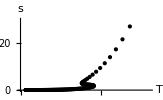
```mathematica
MIN=SetPrecision[MinimumReconstructedPotential/.constants,200];
k11=k1;
k22=k2;
k44=k4;
AbsoluteTiming[
For[ii=-0.9(*0.1*),ii≤5.0(*2.3*),ii+=0.05,
k1=k11;
k2=k22;
k4=k44;
For[jj=0,jj≤0,jj+=1.0(*0.5*),

Monitor[ϕH=SetPrecision[MIN((Tanh[ii]+1)/2),200];
Φmax=√((-2(V[ϕϕ[r]]/.ϕϕ[r]->ϕH ))/ff[ϕH])/.constants;
Φ11=SetPrecision[jj(Φmax/50),200];
Τ=ΒΗs[ϕH,Φ11];(*It is better to construct the normalized solutions, such that Λ=1 at infinity*)
(*{SOL,T,s,pp,ϵϵ,ϕA,ϕB,ϕΗ,nn1,nn2,VEVoverΛ3,μ, ρ}*)
AppendTo[Tlist,{Τ⟦2⟧,Τ⟦3⟧,Τ⟦3⟧/Τ⟦2⟧^3,Log[Τ⟦3⟧],Log[Τ⟦2⟧],-Τ⟦4⟧,Τ⟦4⟧,Τ⟦5⟧,Τ⟦8⟧,Τ⟦7⟧,Τ⟦6⟧,4 Τ⟦7⟧/Τ⟦6⟧^3+1/6,CForm[Τ⟦5⟧],CForm[4 Τ⟦7⟧/Τ⟦6⟧^3+1/6],Τ⟦12⟧,Τ⟦13⟧,Τ⟦9⟧}];
If[jj==0, {k11=k1,k22=k2,k44=k4},0],
(*Print[{"ii=" ii,"jj=" jj}];*)
{{ ii, jj,N[k1],N[k2],N[k4]},Show[-Graphics-,ListPlot[Tlist[[All,{1,2}]],PlotStyle->Red,AxesLabel->{"T/Λ","s/Λ^3"}],ImageSize->600]}]

];
];]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (40.).

FindRoot::precw: The precision of the argument function (Power[E, 0.99997143663851062456160434521734714508056640625000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (-4.03959676635753978780372475757679 + 4.05030491<<26>>86978 r)] <<1>> == 0) is less than WorkingPrecision (90.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 90. digits of working precision to meet these tolerances.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (40.).

FindRoot::precw: The precision of the argument function (Power[E, 0.99997143663851062456160434521734714508056640625000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (-4.04699037106441163735557899117671 + 4.05967808<<26>>39306 r)] <<1>> == 0) is less than WorkingPrecision (90.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 90. digits of working precision to meet these tolerances.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (40.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Power[E, 0.99997143663851062456160434521734714508056640625000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (-4.05563675124212733964497940761532 + 4.07062572<<26>>15773 r)] <<1>> == 0) is less than WorkingPrecision (90.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 90. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{12770.9,Null}

```mathematica
SofT = Tlist[[All,{1,2}]];
```

```mathematica
(*Export["recovered_sofTphiM0_7.txt",SofT,"Table","FieldSeparators"->" "]*)
```

```mathematica
xx=Tlist[[All,{1,2}]];
xx[[All,1]]=xx[[All,1]]-0.002
```

{1.06357,0.975953,0.897009,0.826054,0.762476,0.70571,0.655242,0.610663,0.57161,0.537769,0.508829,0.484543,0.464552,0.448541,0.436176,0.427098,0.420932,0.417302,0.415841,0.416177,0.417963,0.420856,0.424535,0.428695,0.433046,0.437318,0.441272,0.444697,0.447416,0.449289,0.450208,0.450109,0.448956,0.446749,0.443513,0.439296,0.434158,0.428171,0.421416,0.413982,0.405951,0.397411,0.388442,0.379124,0.369527,0.35972,0.349764,0.339719,0.329633,0.319557,0.30953,0.299584,0.289759,0.280071,0.270531,0.261186,0.252048,0.243125,0.234366,0.225862,0.217611,0.209612,0.201866,0.194371,0.187124,0.180122,0.17336,0.166833,0.160536,0.154462,0.148605,0.14296,0.13752,0.132277,0.127227,0.122363,0.117679,0.113168,0.108824,0.104642,0.100616,0.0967408,0.0930104,0.0894199,0.0859641,0.0826381,0.0794371,0.0763567,0.0733923,0.0705395,0.0677944,0.0651528,0.062611,0.0601651,0.0578116,0.0555471,0.0533682,0.0512716,0.0492543,0.0473133,0.0454457,0.0436488,0.0419199,0.0402565,0.0386559,0.037116,0.0356344,0.0342088,0.0328373,0.0315176,0.030248,0.0290264,0.0278511,0.0267203,0.0256323,0.0245855,0.0235784,0.0226094,0.0216771}

```mathematica
Export["/Users/pedro/Desktop/PhD Pedro/Flatten the metric/MH UR paper/0.9 TL/SofT_0_9_epoch_5100000_Vpts_1000_V2.txt",Tlist[[All,{1,2}]],"Table","FieldSeparators"->" "]
```

/Users/pedro/Desktop/PhD Pedro/Flatten the metric/MH UR paper/0.9 TL/SofT_0_9_epoch_5100000_Vpts_1000_V2.txt

#### Results

```mathematica
(*potentialV_3of5*)
```

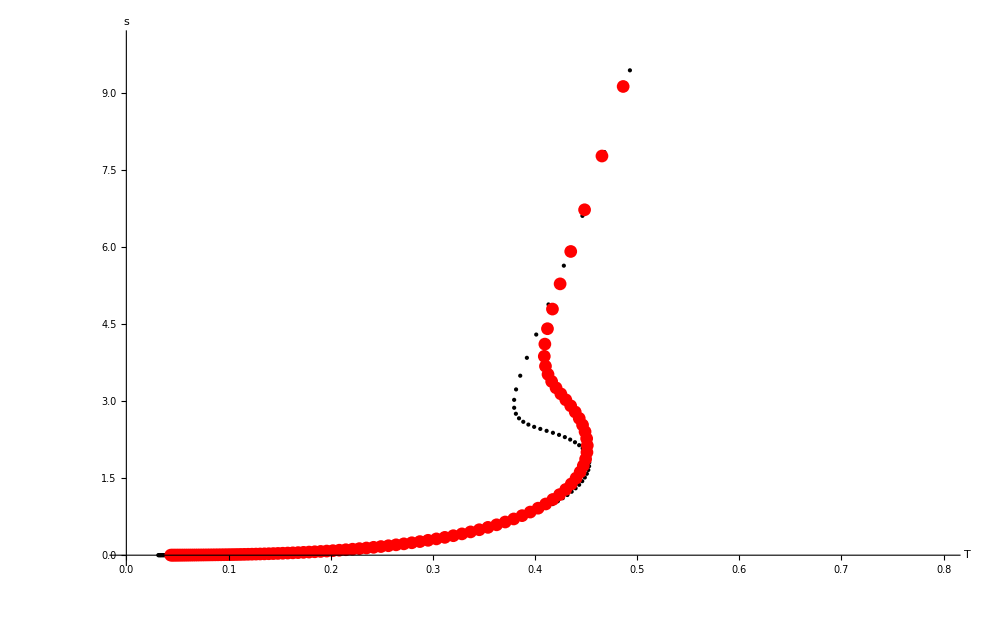

```mathematica
Show[-Graphics-,ListPlot[Tlist[[All,{1,2}]],PlotStyle->Red,AxesLabel->{"T/Λ","s/Λ^3"}],ImageSize->1000,PlotRange->{{0,0.8},{0,10}}]
```

```mathematica
soverT3= Map[{#[[1]],#[[2]]/#[[1]]^3}&, xx ];
```

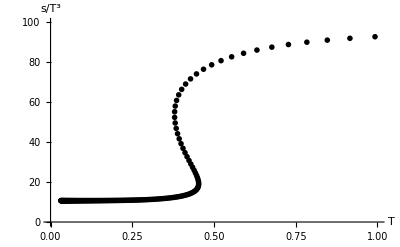
```mathematica
Show[-Graphics-,ListPlot[soverT3,PlotStyle->Red,AxesLabel->{"T/Λ","s/Λ^3"}],ImageSize->600,PlotRange->{{0,1.5},{0,100}}]
```

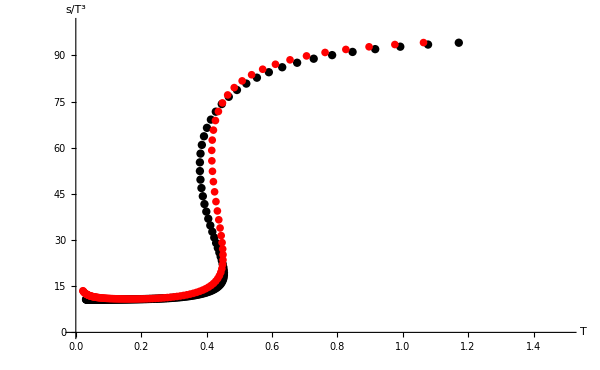

#### Im going to import the curve to do the interpolation, and do . The problem is that, at the phase transition, there are points of the theory that cannot be compared to points of the NN because it doesn’t “reach”. What we do, we flip the s(T)’s 90 degrees, and thus now they can be compared.

```mathematica
Clear[sofTϕM1]
```

```mathematica
sofTϕM1 = Import["/Users/pablo/Desktop/NNholo/MH_flattening_paper_3_to_1/Data/Potentials_phim/SofTphiM0_9.txt","Table"];
sofTϕM1 =Select[sofTϕM1 ,Length[#]>0&];
```

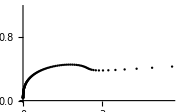

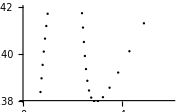

```mathematica
(*Extract x and y values*)
xValues=sofTϕM1 [[All,2]];
yValues=sofTϕM1 [[All,1]];
(*Interpolate*)
SofTOrig=Interpolation[Transpose[{xValues,yValues}]];
a = ListPlot[SofTOrig, PlotStyle->Black]
b = ListPlot[SofTOrig, PlotStyle->Black,PlotRange->{{0,6},{0.38,0.42}}]
```

```mathematica
Clear[sofTrecovered]
sofTrecovered = Import["/Users/pablo/Desktop/NNholo/MH_flattening_paper_3_to_1/flat_5_heads/results_2/pedros_NON_flat/recover_09_forced.txt", "Table"];
```

```mathematica
xxg=sofTrecovered[[All,2]];
yyg=sofTrecovered[[All,1]];
```

```mathematica
sofTrecovered[[1]]
```

{1.2388412884694626924096033000474,179.94908173185002340428360491877}

```mathematica
recoveredsofT=Transpose[{yyg,xxg}];
```

```mathematica
recoveredsoverT3=Map[{#[[1]],#[[2]]/(#[[1]])^3}&,recoveredsofT];
```

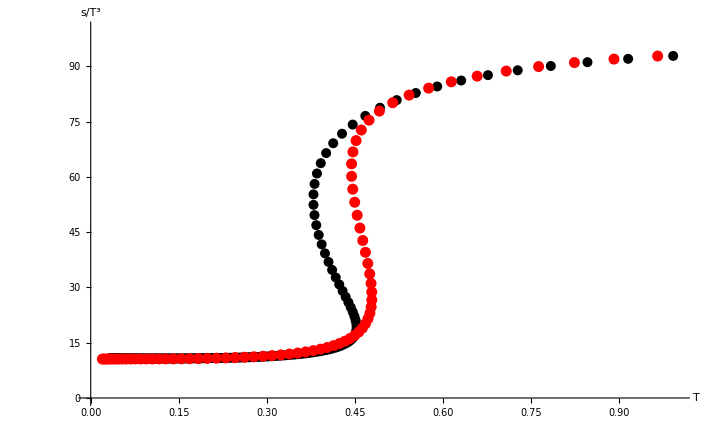

```mathematica
Show[-Graphics-,ListPlot[recoveredsoverT3,PlotStyle->Red]]
```

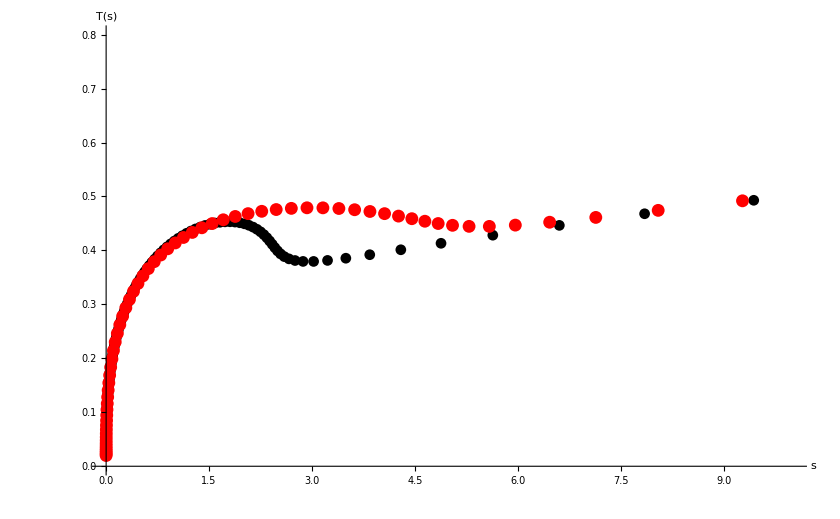

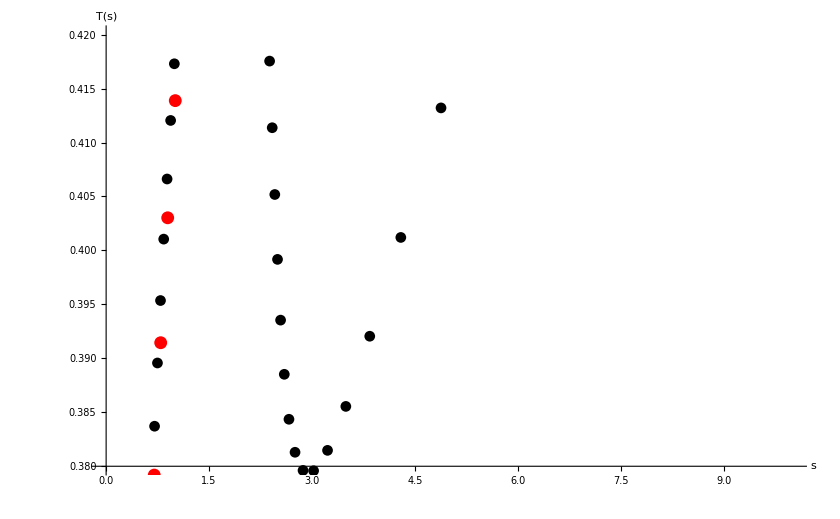

```mathematica
SofTNN = Interpolation[Transpose[{xxg,yyg}]];
Show[a,ListPlot[SofTNN,PlotStyle->Red],PlotRange->{{0,10},{0,0.8}}, AxesLabel->{"s", "T(s)"}]
Show[b, ListPlot[SofTNN, PlotStyle->Red],PlotRange->{{0,10},{0.38,0.42}}, AxesLabel->{"s", "T(s)"}]
```

```mathematica
Clear[Diff,ST3Orig,ST3NN]
```

```mathematica
Diff = {};ST3Orig = {}; ST3NN = {};
For[i =0.001, i<=30,If[i<=6,i+=0.001,i+=0.1], AppendTo[Diff,{i,(Abs[SofTOrig[i]-SofTNN[i]]/SofTOrig[i])*100}];
AppendTo[ST3Orig, {i,SofTOrig[i]/i^3}];
AppendTo[ST3NN,{i,SofTNN[i]/i^3}];
]
```

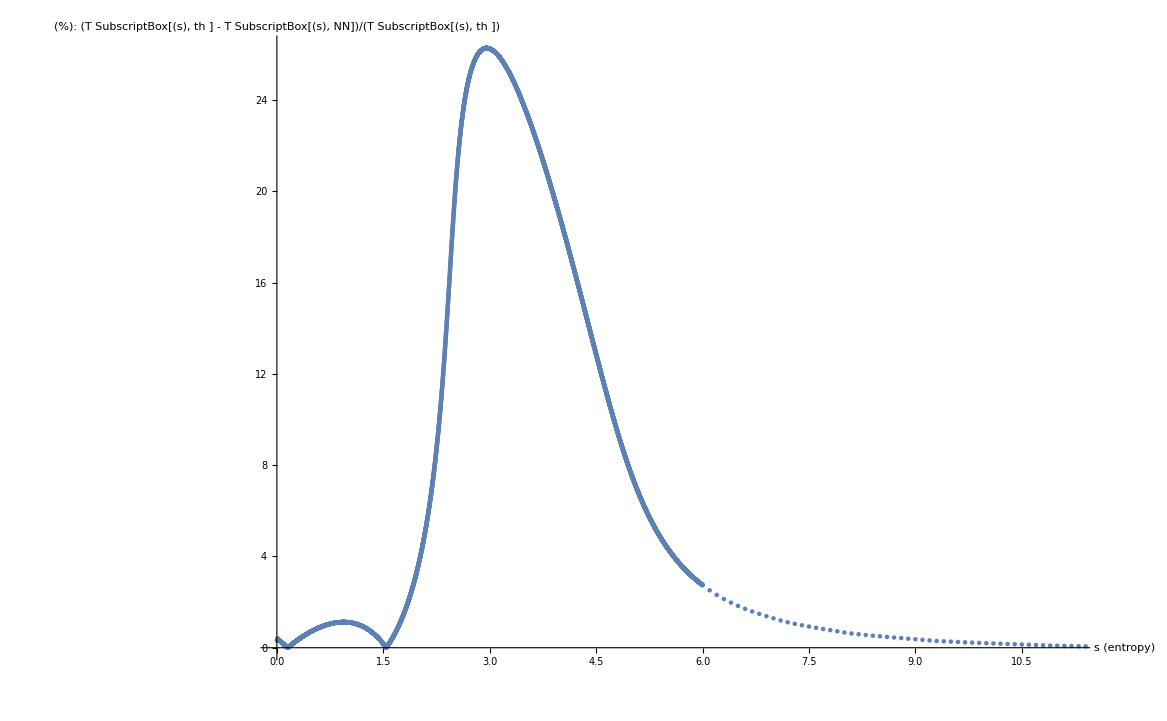

```mathematica
ListPlot[Diff, AxesLabel->{"s (entropy)", "(%): (T SubscriptBox[(s), th ] - T SubscriptBox[(s), NN])/(T SubscriptBox[(s), th ])"}]
```

```mathematica
Export["/Users/pablo/Desktop/NNholo/MH_flattening_paper_3_to_1/flat_5_heads/results_2/pedros_NON_flat/rel_error_sofT_non_flat.csv",Diff,"CSV"];
```

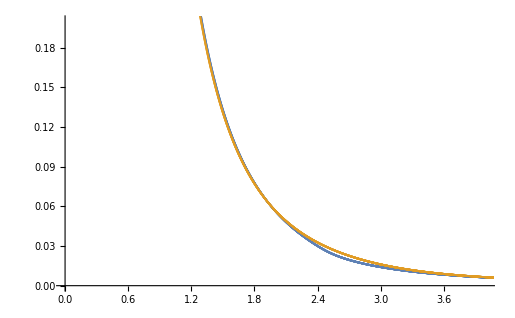

```mathematica
ListPlot[{ST3Orig,ST3NN}, PlotRange->{{0,4},{0,0.2}}]
```

```mathematica
(*potentialV_3of5*)
```

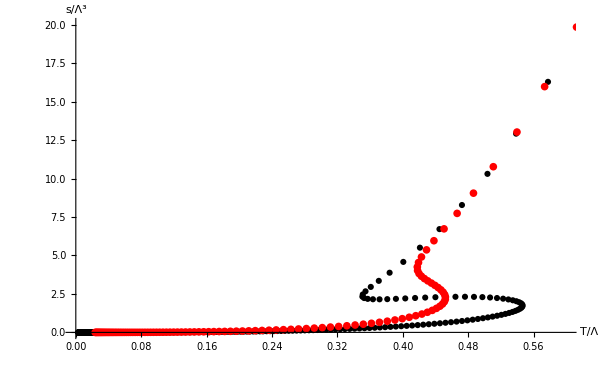

```mathematica
Show[-Graphics-,ListPlot[Tlist[[All,{1,2}]],PlotStyle->Red,AxesLabel->{"T/Λ","s/Λ^3"}],ImageSize->600,PlotRange->{{0,0.6},{0,20}}]
```